## ADAPTIVE BALANCING - 5R MECHANISM

## DEFINITIONS

### RR SUBSYSTEM

```mathematica
(*-Coordinates and quasivelocities-*)
Subscript[𝕢, "RR"][t_]={Subscript[q, "RR",Subscript[ℛ, 1]][t],Subscript[q, "RR",Subscript[ℛ, 2]][t],Subscript[q, "RR",Subscript[𝓅, 2],1][t],Subscript[q, "RR",Subscript[𝓅, 2],2][t],Subscript[q, "RR",Subscript[𝓅, 3],1][t],Subscript[q, "RR",Subscript[𝓅, 3],2][t]};
Subscript[𝕡, "RR"][t_]={Subscript[p, "RR",Subscript[ℛ, 1]][t],Subscript[p, "RR",Subscript[ℛ, 2]][t],Subscript[p, "RR",Subscript[ℬ, 1],1][t],Subscript[p, "RR",Subscript[ℬ, 1],2][t],Subscript[p, "RR",Subscript[ℬ, 1],3][t],Subscript[p, "RR",Subscript[ℬ, 2],1][t],Subscript[p, "RR",Subscript[ℬ, 2],2][t],Subscript[p, "RR",Subscript[ℬ, 2],3][t]};
```

```mathematica
(*-Inertia matrix-*)
Subscript[𝕄, "RR"][t_]=DiagonalMatrix[{0,0,Subscript[m, "RR",Subscript[ℬ, 1]],Subscript[m, "RR",Subscript[ℬ, 1]],Subscript[Ι, "RR",Subscript[ℬ, 1]],Subscript[m, "RR",Subscript[ℬ, 2]],Subscript[m, "RR",Subscript[ℬ, 2]],Subscript[Ι, "RR",Subscript[ℬ, 2]]}];

(*-Giroscopic forces-*)
Subscript[𝕘, "RR"][t_]={0,0,0,0,0,0,0,0};

(*-Active forces-*)
Subscript[𝕗, "RR"][t_]={Subscript[u, "RR",1][t],Subscript[u, "RR",2][t],0,-Subscript[m, "RR",Subscript[ℬ, 1]]g,0,0,-Subscript[m, "RR",Subscript[ℬ, 2]]g,0};
```

```mathematica
(*-Constraint equations-*)
Subscript[𝕔, "RR"][t_]=Flatten[{
Subscript[p, "RR",Subscript[ℛ, 1]][t]-Subscript[q, "RR",Subscript[ℛ, 1]]'[t],
Subscript[p, "RR",Subscript[ℛ, 2]][t]-Subscript[q, "RR",Subscript[ℛ, 2]]'[t],
Flatten[({{Subscript[p, "RR",Subscript[ℬ, 1],1][t]}, {Subscript[p, "RR",Subscript[ℬ, 1],2][t]}})-(1-Subscript[γ, "RR",Subscript[ℬ, 1]])({{0}, {0}})-Subscript[γ, "RR",Subscript[ℬ, 1]]({{Subscript[q, "RR",Subscript[𝓅, 2],1]'[t]}, {Subscript[q, "RR",Subscript[𝓅, 2],2]'[t]}})],
Flatten[({{Subscript[p, "RR",Subscript[ℬ, 2],1][t]}, {Subscript[p, "RR",Subscript[ℬ, 2],2][t]}})-(1-Subscript[γ, "RR",Subscript[ℬ, 2]])({{Subscript[q, "RR",Subscript[𝓅, 2],1]'[t]}, {Subscript[q, "RR",Subscript[𝓅, 2],2]'[t]}})-Subscript[γ, "RR",Subscript[ℬ, 2]]({{Subscript[q, "RR",Subscript[𝓅, 3],1]'[t]}, {Subscript[q, "RR",Subscript[𝓅, 3],2]'[t]}})],
Flatten[({{Subscript[q, "RR",Subscript[𝓅, 2],1]'[t]}, {Subscript[q, "RR",Subscript[𝓅, 2],2]'[t]}})-({{0}, {0}})]-Cross[Flatten[Subscript[p, "RR",Subscript[ℬ, 1],3][t](({{Subscript[q, "RR",Subscript[𝓅, 2],1][t]}, {Subscript[q, "RR",Subscript[𝓅, 2],2][t]}})-({{Subscript[q, "RR",Subscript[𝓅, 1],1]}, {Subscript[q, "RR",Subscript[𝓅, 1],2]}}))]],
Flatten[({{Subscript[q, "RR",Subscript[𝓅, 3],1]'[t]}, {Subscript[q, "RR",Subscript[𝓅, 3],2]'[t]}})-({{Subscript[q, "RR",Subscript[𝓅, 2],1]'[t]}, {Subscript[q, "RR",Subscript[𝓅, 2],2]'[t]}})]-Cross[Flatten[Subscript[p, "RR",Subscript[ℬ, 2],3][t](({{Subscript[q, "RR",Subscript[𝓅, 3],1][t]}, {Subscript[q, "RR",Subscript[𝓅, 3],2][t]}})-({{Subscript[q, "RR",Subscript[𝓅, 2],1][t]}, {Subscript[q, "RR",Subscript[𝓅, 2],2][t]}}))]],
Subscript[p, "RR",Subscript[ℛ, 1]][t]-Subscript[p, "RR",Subscript[ℬ, 1],3][t],
Subscript[p, "RR",Subscript[ℛ, 1]][t]+Subscript[p, "RR",Subscript[ℛ, 2]][t]-Subscript[p, "RR",Subscript[ℬ, 2],3][t]
}];
((𝕢̇)^★)_("RR")[t_]=Flatten@Solve[(#==0)&/@(Subscript[𝕔, "RR"][t]⟦1;;#⟧&@@Dimensions[Subscript[𝕢, "RR"]'[t]]),Subscript[𝕢, "RR"]'[t]];
(𝕔^★)_("RR")[t_]=If[#==={},{0},#]&@DeleteCases[FullSimplify[Subscript[𝕔, "RR"][t]/.((𝕢̇)^★)_("RR")[t]],0];
```

```mathematica
(*-Constraint Matrix-*)
Subscript[𝔸, "RR"][t_]=FullSimplify[D[(𝕔^★)_("RR")[t],{Subscript[𝕡, "RR"][t]}]];
Subscript[𝕓, "RR"][t_]=FullSimplify[D[(𝕔^★)_("RR")[t],t]-Subscript[𝔸, "RR"][t].Subscript[𝕡, "RR"]'[t]];
Subscript[ℂ, "RR"][t_]=Transpose[FullSimplify@RowReduce[NullSpace[Subscript[𝔸, "RR"][t]]]];
Subscript[ℂ, "RR"][t]//MatrixForm
Norm[Subscript[𝔸, "RR"][t].Subscript[ℂ, "RR"][t]//FullSimplify]
```

(1 | 0
0 | 1
γ_(RR,ℬ_1) (q_(RR,𝓅_1,2)-q_(RR,𝓅_2,2)[t]) | 0
γ_(RR,ℬ_1) (-q_(RR,𝓅_1,1)+q_(RR,𝓅_2,1)[t]) | 0
1 | 0
q_(RR,𝓅_1,2)+(-1+γ_(RR,ℬ_2)) q_(RR,𝓅_2,2)[t]-γ_(RR,ℬ_2) q_(RR,𝓅_3,2)[t] | γ_(RR,ℬ_2) (q_(RR,𝓅_2,2)[t]-q_(RR,𝓅_3,2)[t])
-q_(RR,𝓅_1,1)-(-1+γ_(RR,ℬ_2)) q_(RR,𝓅_2,1)[t]+γ_(RR,ℬ_2) q_(RR,𝓅_3,1)[t] | γ_(RR,ℬ_2) (-q_(RR,𝓅_2,1)[t]+q_(RR,𝓅_3,1)[t])
1 | 1)

0

```mathematica
(*-Dynamic equations-*)
Subscript[𝕕, "RR"][t_]=FullSimplify[Transpose[Subscript[ℂ, "RR"][t]].(-Subscript[𝕄, "RR"][t].Subscript[𝕡, "RR"]'[t]+Subscript[𝕘, "RR"][t]+Subscript[𝕗, "RR"][t])];
(*Subscript[𝕕, "RR"][t]//TableForm*)
```

### PAYLOAD SUBSYSTEM / ROTOR SUBSYSTEM

```mathematica
(*-Coordinates and quasivelocities-*)
Subscript[𝕢, "PL"][t_]={Subscript[q, "PL",Subscript[𝓅, 1],1][t],Subscript[q, "PL",Subscript[𝓅, 1],2][t]};
Subscript[𝕡, "PL"][t_]={Subscript[p, "PL",Subscript[ℬ, 1],1][t],Subscript[p, "PL",Subscript[ℬ, 1],2][t],Subscript[p, "PL",Subscript[ℬ, 1],3][t]};
```

```mathematica
(*-Inertia matrix-*)
Subscript[𝕄, "PL"][t_]=DiagonalMatrix[{Subscript[m, "PL",Subscript[ℬ, 1]],Subscript[m, "PL",Subscript[ℬ, 1]],Subscript[Ι, "PL",Subscript[ℬ, 1]]}];

(*-Giroscopic forces-*)
Subscript[𝕘, "PL"][t_]={0,0,0};

(*-Active forces-*)
Subscript[𝕗, "PL"][t_]={0,-Subscript[m, "PL",Subscript[ℬ, 1]]g,0};
```

```mathematica
(*-Constraint equations-*)
Subscript[𝕔, "PL"][t_]=Flatten[{
Subscript[p, "PL",Subscript[ℬ, 1],1][t]-Subscript[q, "PL",Subscript[𝓅, 1],1]'[t],
Subscript[p, "PL",Subscript[ℬ, 1],2][t]-Subscript[q, "PL",Subscript[𝓅, 1],2]'[t]
}];
((𝕢̇)^★)_("PL")[t_]=Flatten@Solve[(#==0)&/@(Subscript[𝕔, "PL"][t]⟦1;;#⟧&@@Dimensions[Subscript[𝕢, "PL"]'[t]]),Subscript[𝕢, "PL"]'[t]];
(𝕔^★)_("PL")[t_]=If[#==={},{0},#]&@DeleteCases[FullSimplify[Subscript[𝕔, "PL"][t]/.((𝕢̇)^★)_("PL")[t]],0];
```

```mathematica
(*-Constraint Matrix-*)
Subscript[𝔸, "PL"][t_]=FullSimplify[D[(𝕔^★)_("PL")[t],{Subscript[𝕡, "PL"][t]}]];
Subscript[𝕓, "PL"][t_]=FullSimplify[D[(𝕔^★)_("PL")[t],t]-Subscript[𝔸, "PL"][t].Subscript[𝕡, "PL"]'[t]];
Subscript[ℂ, "PL"][t_]=Transpose[FullSimplify@RowReduce[NullSpace[Subscript[𝔸, "PL"][t]]]];
Subscript[ℂ, "PL"][t]//MatrixForm
Norm[Subscript[𝔸, "PL"][t].Subscript[ℂ, "PL"][t]//FullSimplify]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

0

```mathematica
(*-Dynamic equations-*)
Subscript[𝕕, "PL"][t_]=FullSimplify[Transpose[Subscript[ℂ, "PL"][t]].(-Subscript[𝕄, "PL"][t].Subscript[𝕡, "PL"]'[t]+Subscript[𝕘, "PL"][t]+Subscript[𝕗, "PL"][t])];
(*Subscript[𝕕, "PL"][t]//TableForm*)
```

### COMPENSATION INERTIA SUBSYSTEM

```mathematica
(*-Coordinates and quasivelocities-*)
Subscript[𝕢, "BI"][t_]={Subscript[q, "BI",Subscript[𝓅, 1],1][t],Subscript[q, "BI",Subscript[𝓅, 1],2][t]};
Subscript[𝕡, "BI"][t_]={Subscript[p, "BI",Subscript[ℬ, 1],1][t],Subscript[p, "BI",Subscript[ℬ, 1],2][t]};
```

```mathematica
(*-Inertia matrix-*)
Subscript[𝕄, "BI"][t_]=DiagonalMatrix[{Subscript[m, "BI",Subscript[ℬ, 1]],Subscript[m, "BI",Subscript[ℬ, 1]]}];

(*-Giroscopic forces-*)
Subscript[𝕘, "BI"][t_]={0,0};

(*-Active forces-*)
Subscript[𝕗, "BI"][t_]={0,-Subscript[m, "BI",Subscript[ℬ, 1]]g};
```

```mathematica
(*-Constraint equations-*)
Subscript[𝕔, "BI"][t_]=Flatten[{
Subscript[p, "BI",Subscript[ℬ, 1],1][t]-Subscript[q, "BI",Subscript[𝓅, 1],1]'[t],
Subscript[p, "BI",Subscript[ℬ, 1],2][t]-Subscript[q, "BI",Subscript[𝓅, 1],2]'[t]
}];
((𝕢̇)^★)_("BI")[t_]=Flatten@Solve[(#==0)&/@(Subscript[𝕔, "BI"][t]⟦1;;#⟧&@@Dimensions[Subscript[𝕢, "BI"]'[t]]),Subscript[𝕢, "BI"]'[t]];
(𝕔^★)_("BI")[t_]=If[#==={},{0},#]&@DeleteCases[FullSimplify[Subscript[𝕔, "BI"][t]/.((𝕢̇)^★)_("BI")[t]],0];
```

```mathematica
(*-Constraint Matrix-*)
Subscript[𝔸, "BI"][t_]=FullSimplify[D[(𝕔^★)_("BI")[t],{Subscript[𝕡, "BI"][t]}]];
Subscript[𝕓, "BI"][t_]=FullSimplify[D[(𝕔^★)_("BI")[t],t]-Subscript[𝔸, "BI"][t].Subscript[𝕡, "BI"]'[t]];
Subscript[ℂ, "BI"][t_]=Transpose[FullSimplify@RowReduce[NullSpace[Subscript[𝔸, "BI"][t]]]];
Subscript[ℂ, "BI"][t]//MatrixForm
Norm[Subscript[𝔸, "BI"][t].Subscript[ℂ, "BI"][t]//FullSimplify]
```

(1 | 0
0 | 1)

0

```mathematica
(*-Dynamic equations-*)
Subscript[𝕕, "BI"][t_]=FullSimplify[Transpose[Subscript[ℂ, "BI"][t]].(-Subscript[𝕄, "BI"][t].Subscript[𝕡, "BI"]'[t]+Subscript[𝕘, "BI"][t]+Subscript[𝕗, "BI"][t])];
(*Subscript[𝕕, "BI"][t]//TableForm*)
```

### AUXILIARY FUNCTIONS

```mathematica
Coeff={♢u,♢f, ♢p}↦(#-> Module[{♢a,♢b},♢a=FullSimplify[Normal@CoefficientArrays[#/.♢f,D[♢p,t],"Symmetric"-> True]];
♢b=FullSimplify[Normal@CoefficientArrays[Flatten[♢a⟦1⟧],♢p,"Symmetric"-> True]];
Join[Flatten@{♢a⟦2⟧},Flatten@{♢b⟦3⟧},Flatten@{♢b⟦2⟧},Flatten@{♢b⟦1⟧}]])&/@♢u;
(*Coeff[{y[t]},{y[t]-> Subscript[a, 1] Subscript[x, 1]'[t]+Subscript[a, 2] Subscript[x, 2]'[t]+Subscript[b, 1] (Subscript[x, 1][t])^2+2 Subscript[b, 12] Subscript[x, 1][t] Subscript[x, 2][t]+Subscript[b, 2] (Subscript[x, 2][t])^2+Subscript[c, 1] Subscript[x, 1][t]+Subscript[c, 2] Subscript[x, 2][t]+d},{Subscript[x, 1][t],Subscript[x, 2][t]}]*)
```

```mathematica
Subsystem={♢system,♢number,♢type}↦(
𝕢_(♢system,♢number)[t_]=𝕢_(♢type)[t]/.{♢type->♢number};
𝕡_(♢system,♢number)[t_]=𝕡_(♢type)[t]/.{♢type->♢number};
𝕄_(♢system,♢number)[t_]=𝕄_(♢type)[t]/.{♢type->♢number};
𝕘_(♢system,♢number)[t_]=𝕘_(♢type)[t]/.{♢type->♢number};
𝕗_(♢system,♢number)[t_]=𝕗_(♢type)[t]/.{♢type->♢number};
(𝕔^★)_(♢system,♢number)[t_]=(𝕔^★)_(♢type)[t]/.{♢type->♢number};
((𝕢̇)^★)_(♢system,♢number)[t_]=((𝕢̇)^★)_(♢type)[t]/.{♢type->♢number};
𝔸_(♢system,♢number)[t_]=𝔸_(♢type)[t]/.{♢type->♢number};
𝕓_(♢system,♢number)[t_]=𝕓_(♢type)[t]/.{♢type->♢number};
ℂ_(♢system,♢number)[t_]=ℂ_(♢type)[t]/.{♢type->♢number};
𝕕_(♢system,♢number)[t_]=𝕕_(♢type)[t]/.{♢type->♢number};);
```

```mathematica
SignA=2/π ArcTan[5 31.820 #]&;
```

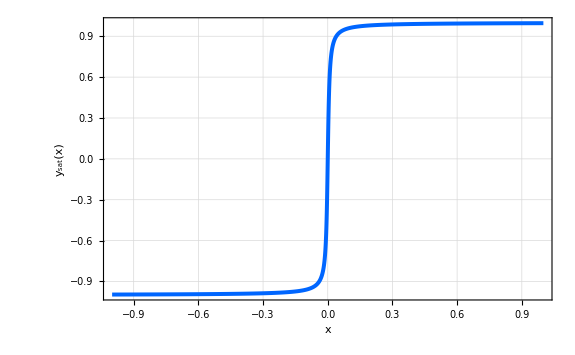
-Graphics-
-Graphics-

```mathematica
SPlot[SignA[t],{t,-1,1},{"x","y_sat(x)"},"",{}]
```

```mathematica
Cycloid=Function[{t,T},t/T-1/(2π)Sin[2π t/T]];
```

### PLOTTING FUNCTIONS

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->16}];
SetOptions[Plot3D,BaseStyle->{FontFamily->"Arial",FontSize->14}];
SetOptions[ParametricPlot,BaseStyle->{FontFamily->"Arial",FontSize->16}];
SetOptions[ParametricPlot3D,BaseStyle->{FontFamily->"Arial",FontSize->14}];
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->16}];
Style8={{Hue[0.6,1,1],Thickness[0.005]},{Hue[0.3,1,1],Thickness[0.006],Dashed},{Hue[1,1,1],Thickness[0.007],Dotted},{Hue[0.1,1,1],Thickness[0.005]},{Hue[0.9,1,1],Thickness[0.006],Dashed},{Hue[0.5,1,1],Thickness[0.007],Dotted},{Hue[0.2,1,1],Thickness[0.005]},{Hue[0.8,1,1],Thickness[0.006],Dashed}};

SPlot=Module[{st=Style8},TableForm[{Plot[#1,#2,PlotStyle->Style8,PlotRange->Full,Frame->True,FrameLabel->#3,PlotLabel->#4,GridLines->Automatic,ImageSize->1.15 {500,300}],Graphics[{Black,Directive[FontFamily->"Arial",FontSize->16],MapIndexed[Text[#1,{10(First[#2]-1)+6,0}]&,#5],MapIndexed[Join[Last[st=RotateLeft@st],{Line[{{10(First[#2]-1),0},{10(First[#2]-1)+3,0}}]}]&,#5]},ImageSize->1.15 {500,30}]}]]&;
```

## UNBALANCED AND STATICALLY BALANCED RR MECHANISMS

### COMPLETE RR MODEL (RR_)

```mathematica
(*-Subsystems-*)
Subscript[Σ, "RR_"]={1,2,3,4};
Subsystem["RR_",1,"RR"] (*Subsystem 1: RR*)
Subsystem["RR_",2,"PL"] (*Subsystem 2: Payload*)
Subsystem["RR_",3,"BI"] (*Subsystem 3: Compensation inertia*)
Subsystem["RR_",4,"BI"] (*Subsystem 4: Compensation inertia*)

(*-System Variables-*)
Subscript[𝕢, "RR_"][t_]=Join@@(Subscript[𝕢, "RR_",#][t]&/@Subscript[Σ, "RR_"]);
Subscript[𝕡, "RR_"][t_]=Join@@(Subscript[𝕡, "RR_",#][t]&/@Subscript[Σ, "RR_"]);
```

```mathematica
(*-Additional constraints-*)
((𝕢̇)^★)_("RR_")[t_]=Join@@(((𝕢̇)^★)_("RR_",#)[t]&/@Subscript[Σ, "RR_"]);
(𝕔^♁)_("RR_") [t_]=({Subscript[q, 1,Subscript[𝓅, 3],1]'[t]-Subscript[q, 2,Subscript[𝓅, 1],1]'[t],Subscript[q, 1,Subscript[𝓅, 3],2]'[t]-Subscript[q, 2,Subscript[𝓅, 1],2]'[t],Subscript[p, 1,Subscript[ℬ, 2],3][t]-Subscript[p, 2,Subscript[ℬ, 1],3][t],Subscript[q, 3,Subscript[𝓅, 1],1]'[t]+Subscript[γ, 3,Subscript[ℬ, 1]] Subscript[q, 1,Subscript[𝓅, 2],1]'[t],Subscript[q, 3,Subscript[𝓅, 1],2]'[t]+Subscript[γ, 3,Subscript[ℬ, 1]] Subscript[q, 1,Subscript[𝓅, 2],2]'[t],(Subscript[q, 4,Subscript[𝓅, 1],1]'[t]-Subscript[q, 1,Subscript[𝓅, 2],1]'[t])+Subscript[γ, 4,Subscript[ℬ, 1]](Subscript[q, 1,Subscript[𝓅, 3],1]'[t]-Subscript[q, 1,Subscript[𝓅, 2],1]'[t]),(Subscript[q, 4,Subscript[𝓅, 1],2]'[t]-Subscript[q, 1,Subscript[𝓅, 2],2]'[t])+Subscript[γ, 4,Subscript[ℬ, 1]](Subscript[q, 1,Subscript[𝓅, 3],2]'[t]-Subscript[q, 1,Subscript[𝓅, 2],2]'[t])}/.((𝕢̇)^★)_("RR_")[t]);
(𝕔^★)_("RR_")[t_]=DeleteCases[Join[Join@@((𝕔^★)_("RR_",#)[t]&/@Subscript[Σ, "RR_"]),(𝕔^♁)_("RR_") [t]],0];

(*-Additional constraints matrix-*)
Subscript[𝔹, "RR_"][t_]=Transpose@(Join@@(Transpose@FullSimplify[D[(𝕔^♁)_("RR_") [t],{Subscript[𝕡, "RR_",#][t]}].Subscript[ℂ, "RR_",#][t]]&/@Subscript[Σ, "RR_"]));
Subscript[ℂ, "RR_"][t_]=Transpose[FullSimplify@RowReduce[NullSpace[Subscript[𝔹, "RR_"][t]]]];
Subscript[ℂ, "RR_"][t]//MatrixForm
Norm[Subscript[𝔹, "RR_"][t].Subscript[ℂ, "RR_"][t]//FullSimplify]
```

(1 | 0
0 | 1
q_(1,𝓅_1,2)-q_(1,𝓅_3,2)[t] | q_(1,𝓅_2,2)[t]-q_(1,𝓅_3,2)[t]
-q_(1,𝓅_1,1)+q_(1,𝓅_3,1)[t] | -q_(1,𝓅_2,1)[t]+q_(1,𝓅_3,1)[t]
1 | 1
γ_(3,ℬ_1) (-q_(1,𝓅_1,2)+q_(1,𝓅_2,2)[t]) | 0
γ_(3,ℬ_1) (q_(1,𝓅_1,1)-q_(1,𝓅_2,1)[t]) | 0
q_(1,𝓅_1,2)-(1+γ_(4,ℬ_1)) q_(1,𝓅_2,2)[t]+γ_(4,ℬ_1) q_(1,𝓅_3,2)[t] | γ_(4,ℬ_1) (-q_(1,𝓅_2,2)[t]+q_(1,𝓅_3,2)[t])
-q_(1,𝓅_1,1)+(1+γ_(4,ℬ_1)) q_(1,𝓅_2,1)[t]-γ_(4,ℬ_1) q_(1,𝓅_3,1)[t] | γ_(4,ℬ_1) (q_(1,𝓅_2,1)[t]-q_(1,𝓅_3,1)[t]))

0

```mathematica
(*-Dynamic equations-*)
Subscript[𝕕, "RR_"][t_]=FullSimplify[Transpose[Subscript[ℂ, "RR_"][t]].Join@@(Subscript[𝕕, "RR_",#][t]&/@Subscript[Σ, "RR_"])];
```

```mathematica
(*-Inverse dynamics solution-*)
Subscript[𝕡^#, "RR_"][t_]={Subscript[p, 1,Subscript[ℛ, 1]][t],Subscript[p, 1,Subscript[ℛ, 2]][t]};
Subscript[𝕦^#, "RR_"][t_]={Subscript[u, 1,1][t],Subscript[u, 1,2][t]};
(𝕡^★)_("RR_")[t_]=FullSimplify[Join[#,D[#,t]/.((𝕢̇)^★)_("RR_")[t]/.#]&@Flatten@Solve[(#==0)&/@(𝕔^★)_("RR_")[t],Complement[Subscript[𝕡, "RR_"][t],Subscript[𝕡^#, "RR_"][t]]]];
(𝕢^★)_("RR_")[t_]={Subscript[q, 1,Subscript[𝓅, 1],1]-> 0,Subscript[q, 1,Subscript[𝓅, 1],2]-> 0,Subscript[q, 1,Subscript[𝓅, 2],1][t]-> Subscript[a, 1] Cos[Subscript[q, 1,Subscript[ℛ, 1]][t]],Subscript[q, 1,Subscript[𝓅, 2],2][t]-> Subscript[a, 1] Sin[Subscript[q, 1,Subscript[ℛ, 1]][t]],Subscript[q, 1,Subscript[𝓅, 3],1][t]-> Subscript[a, 1] Cos[Subscript[q, 1,Subscript[ℛ, 1]][t]]+Subscript[a, 2] Cos[Subscript[q, 1,Subscript[ℛ, 1]][t]+Subscript[q, 1,Subscript[ℛ, 2]][t]],Subscript[q, 1,Subscript[𝓅, 3],2][t]-> Subscript[a, 1] Sin[Subscript[q, 1,Subscript[ℛ, 1]][t]]+Subscript[a, 2] Sin[Subscript[q, 1,Subscript[ℛ, 1]][t]+Subscript[q, 1,Subscript[ℛ, 2]][t]]};
(𝕦^★)_("RR_")[t_]=Flatten[Solve[(#==0)&/@FullSimplify[Subscript[𝕕, "RR_"][t]/.(𝕡^★)_("RR_")[t]/.(𝕢^★)_("RR_")[t]],Subscript[𝕦^#, "RR_"][t]]];
Subscript[𝕦^(★©), "RR_"][t_]=Coeff[Subscript[𝕦^#, "RR_"][t],(𝕦^★)_("RR_")[t],Subscript[𝕡^#, "RR_"][t]];
(Print[StringForm["*-- `` Coefficients --*\n",#],#/.Subscript[𝕦^(★©), "RR_"][t]//TableForm,"\n"])&/@Subscript[𝕦^#, "RR_"][t];
```

*-- u_1, 1[t] Coefficients --*
a_1^2 (m_(1,ℬ_2)+m_(2,ℬ_1)+m_(4,ℬ_1)+m_(1,ℬ_1) γ_(1,ℬ_1)^2+m_(3,ℬ_1) γ_(3,ℬ_1)^2)+2 Cos[q_(1,ℛ_2)[t]] a_1 a_2 (m_(2,ℬ_1)+m_(1,ℬ_2) γ_(1,ℬ_2)-m_(4,ℬ_1) γ_(4,ℬ_1))+a_2^2 (m_(2,ℬ_1)+m_(1,ℬ_2) γ_(1,ℬ_2)^2+m_(4,ℬ_1) γ_(4,ℬ_1)^2)+Ι_(1,ℬ_1)+Ι_(1,ℬ_2)+Ι_(2,ℬ_1)
Cos[q_(1,ℛ_2)[t]] a_1 a_2 (m_(2,ℬ_1)+m_(1,ℬ_2) γ_(1,ℬ_2)-m_(4,ℬ_1) γ_(4,ℬ_1))+a_2^2 (m_(2,ℬ_1)+m_(1,ℬ_2) γ_(1,ℬ_2)^2+m_(4,ℬ_1) γ_(4,ℬ_1)^2)+Ι_(1,ℬ_2)+Ι_(2,ℬ_1)
0
-Sin[q_(1,ℛ_2)[t]] a_1 a_2 (m_(2,ℬ_1)+m_(1,ℬ_2) γ_(1,ℬ_2)-m_(4,ℬ_1) γ_(4,ℬ_1))
-Sin[q_(1,ℛ_2)[t]] a_1 a_2 (m_(2,ℬ_1)+m_(1,ℬ_2) γ_(1,ℬ_2)-m_(4,ℬ_1) γ_(4,ℬ_1))
-Sin[q_(1,ℛ_2)[t]] a_1 a_2 (m_(2,ℬ_1)+m_(1,ℬ_2) γ_(1,ℬ_2)-m_(4,ℬ_1) γ_(4,ℬ_1))
0
0
g Cos[q_(1,ℛ_1)[t]] a_1 (m_(1,ℬ_2)+m_(2,ℬ_1)+m_(4,ℬ_1)+m_(1,ℬ_1) γ_(1,ℬ_1)-m_(3,ℬ_1) γ_(3,ℬ_1))+g Cos[q_(1,ℛ_1)[t]+q_(1,ℛ_2)[t]] a_2 (m_(2,ℬ_1)+m_(1,ℬ_2) γ_(1,ℬ_2)-m_(4,ℬ_1) γ_(4,ℬ_1))

*-- u_1, 2[t] Coefficients --*
Cos[q_(1,ℛ_2)[t]] a_1 a_2 (m_(2,ℬ_1)+m_(1,ℬ_2) γ_(1,ℬ_2)-m_(4,ℬ_1) γ_(4,ℬ_1))+a_2^2 (m_(2,ℬ_1)+m_(1,ℬ_2) γ_(1,ℬ_2)^2+m_(4,ℬ_1) γ_(4,ℬ_1)^2)+Ι_(1,ℬ_2)+Ι_(2,ℬ_1)
a_2^2 (m_(2,ℬ_1)+m_(1,ℬ_2) γ_(1,ℬ_2)^2+m_(4,ℬ_1) γ_(4,ℬ_1)^2)+Ι_(1,ℬ_2)+Ι_(2,ℬ_1)
Sin[q_(1,ℛ_2)[t]] a_1 a_2 (m_(2,ℬ_1)+m_(1,ℬ_2) γ_(1,ℬ_2)-m_(4,ℬ_1) γ_(4,ℬ_1))
0
0
0
0
0
g Cos[q_(1,ℛ_1)[t]+q_(1,ℛ_2)[t]] a_2 (m_(2,ℬ_1)+m_(1,ℬ_2) γ_(1,ℬ_2)-m_(4,ℬ_1) γ_(4,ℬ_1))

```mathematica
(*-Unbalanced model-*)
Subscript[𝕒, "RR_U"][t_]={(*Subscript[m, 3,Subscript[ℬ, 1]]-> 0,Subscript[m, 4,Subscript[ℬ, 1]]-> 0,*)Subscript[q, 1,Subscript[ℛ, 1]][t]-> Subscript[q, "RR_U",Subscript[ℛ, 1]][t],Subscript[q, 1,Subscript[ℛ, 2]][t]-> Subscript[q, "RR_U",Subscript[ℛ, 2]][t],(Subscript[a, 2]^2 (Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 2]] Subscript[γ, 1,Subscript[ℬ, 2]]^2+Subscript[m, 4,Subscript[ℬ, 1]] Subscript[γ, 4,Subscript[ℬ, 1]]^2)+Subscript[Ι, 1,Subscript[ℬ, 2]]+Subscript[Ι, 2,Subscript[ℬ, 1]])-> Subscript[Ι, "RR_U",1],(Subscript[a, 1]^2 (Subscript[m, 1,Subscript[ℬ, 2]]+Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 4,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 1]] Subscript[γ, 1,Subscript[ℬ, 1]]^2+Subscript[m, 3,Subscript[ℬ, 1]] Subscript[γ, 3,Subscript[ℬ, 1]]^2))-> Subscript[Ι, "RR_U",2]-Subscript[Ι, 1,Subscript[ℬ, 1]] ,(Subscript[a, 1] Subscript[a, 2] (Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 2]] Subscript[γ, 1,Subscript[ℬ, 2]]-Subscript[m, 4,Subscript[ℬ, 1]] Subscript[γ, 4,Subscript[ℬ, 1]]))->Subscript[Ι, "RR_U",3],(Subscript[a, 1] (Subscript[m, 1,Subscript[ℬ, 2]]+Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 4,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 1]] Subscript[γ, 1,Subscript[ℬ, 1]]-Subscript[m, 3,Subscript[ℬ, 1]] Subscript[γ, 3,Subscript[ℬ, 1]]))-> Subscript[𝓂, "RR_U",1]/g,(Subscript[a, 2] (Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 2]] Subscript[γ, 1,Subscript[ℬ, 2]]-Subscript[m, 4,Subscript[ℬ, 1]] Subscript[γ, 4,Subscript[ℬ, 1]]))-> Subscript[𝓂, "RR_U",2]/g};
(Print[StringForm["*-- `` Coefficients --*\n",#],#/.(Subscript[𝕦^(★©), "RR_"][t]//.Subscript[𝕒, "RR_U"][t])//TableForm,"\n"])&/@Subscript[𝕦^#, "RR_"][t];
```

*-- u_1, 1[t] Coefficients --*
Ι_(RR_U,1)+Ι_(RR_U,2)+2 Cos[q_(RR_U,ℛ_2)[t]] Ι_(RR_U,3)
Ι_(RR_U,1)+Cos[q_(RR_U,ℛ_2)[t]] Ι_(RR_U,3)
0
-Sin[q_(RR_U,ℛ_2)[t]] Ι_(RR_U,3)
-Sin[q_(RR_U,ℛ_2)[t]] Ι_(RR_U,3)
-Sin[q_(RR_U,ℛ_2)[t]] Ι_(RR_U,3)
0
0
Cos[q_(RR_U,ℛ_1)[t]] 𝓂_(RR_U,1)+Cos[q_(RR_U,ℛ_1)[t]+q_(RR_U,ℛ_2)[t]] 𝓂_(RR_U,2)

*-- u_1, 2[t] Coefficients --*
Ι_(RR_U,1)+Cos[q_(RR_U,ℛ_2)[t]] Ι_(RR_U,3)
Ι_(RR_U,1)
Sin[q_(RR_U,ℛ_2)[t]] Ι_(RR_U,3)
0
0
0
0
0
Cos[q_(RR_U,ℛ_1)[t]+q_(RR_U,ℛ_2)[t]] 𝓂_(RR_U,2)

```mathematica
(*-Static balancing-*)
Subscript[𝕒, "RR_S"][t_]={(Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 2]] Subscript[γ, 1,Subscript[ℬ, 2]]-Subscript[m, 4,Subscript[ℬ, 1]] Subscript[γ, 4,Subscript[ℬ, 1]])-> 0,(Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 2]]+Subscript[m, 4,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 1]] Subscript[γ, 1,Subscript[ℬ, 1]]-Subscript[m, 3,Subscript[ℬ, 1]] Subscript[γ, 3,Subscript[ℬ, 1]])-> 0,(Subscript[a, 2]^2 (Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 2]] Subscript[γ, 1,Subscript[ℬ, 2]]^2+Subscript[m, 4,Subscript[ℬ, 1]] Subscript[γ, 4,Subscript[ℬ, 1]]^2)+Subscript[Ι, 1,Subscript[ℬ, 2]]+Subscript[Ι, 2,Subscript[ℬ, 1]])-> Subscript[Ι, "RR_S",1],(Subscript[a, 1]^2 (Subscript[m, 1,Subscript[ℬ, 2]]+Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 4,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 1]] Subscript[γ, 1,Subscript[ℬ, 1]]^2+Subscript[m, 3,Subscript[ℬ, 1]] Subscript[γ, 3,Subscript[ℬ, 1]]^2))-> Subscript[Ι, "RR_S",2]-Subscript[Ι, 1,Subscript[ℬ, 1]]};
(Print[StringForm["*-- `` Coefficients --*\n",#],#/.(Subscript[𝕦^(★©), "RR_"][t]//.Subscript[𝕒, "RR_S"][t])//TableForm,"\n"])&/@Subscript[𝕦^#, "RR_"][t];
```

*-- u_1, 1[t] Coefficients --*
Ι_(RR_S,1)+Ι_(RR_S,2)
Ι_(RR_S,1)
0
0
0
0
0
0
0

*-- u_1, 2[t] Coefficients --*
Ι_(RR_S,1)
Ι_(RR_S,1)
0
0
0
0
0
0
0

### UNBALANCED RR MODEL (RR_U)

```mathematica
(*-Coordinates and quasivelocities-*)
Subscript[𝕢, "RR_U"][t_]={Subscript[q, "RR_U",Subscript[ℛ, 1]][t],Subscript[q, "RR_U",Subscript[ℛ, 2]][t],Subscript[q, "RR_U",Subscript[𝓅, 1],1][t],Subscript[q, "RR_U",Subscript[𝓅, 1],2][t]};
Subscript[𝕡, "RR_U"][t_]={Subscript[p, "RR_U",Subscript[ℛ, 1]][t],Subscript[p, "RR_U",Subscript[ℛ, 2]][t]};
```

```mathematica
(*-Inertia matrix-*)
Subscript[𝕄, "RR_U"][t_]=({{Subscript[Ι, "RR_U",1]+Subscript[Ι, "RR_U",2]+2 Cos[Subscript[q, "RR_U",Subscript[ℛ, 2]][t]] Subscript[Ι, "RR_U",3], Subscript[Ι, "RR_U",1]+Cos[Subscript[q, "RR_U",Subscript[ℛ, 2]][t]] Subscript[Ι, "RR_U",3]}, {Subscript[Ι, "RR_U",1]+Cos[Subscript[q, "RR_U",Subscript[ℛ, 2]][t]] Subscript[Ι, "RR_U",3], Subscript[Ι, "RR_U",1]}});

(*-Giroscopic forces-*)
Subscript[𝕘, "RR_U"][t_]={2 Sin[Subscript[q, "RR_U",Subscript[ℛ, 2]][t]] Subscript[Ι, "RR_U",3] Subscript[p, "RR_U",Subscript[ℛ, 1]][t]Subscript[p, "RR_U",Subscript[ℛ, 2]][t]+Sin[Subscript[q, "RR_U",Subscript[ℛ, 2]][t]] Subscript[Ι, "RR_U",3](Subscript[p, "RR_U",Subscript[ℛ, 2]][t])^2,-Sin[Subscript[q, "RR_U",Subscript[ℛ, 2]][t]] Subscript[Ι, "RR_U",3](Subscript[p, "RR_U",Subscript[ℛ, 1]][t])^2};

(*-Active forces-*)
Subscript[𝕗, "RR_U"][t_]={Subscript[u, "RR_U"][t]-(Cos[Subscript[q, "RR_U",Subscript[ℛ, 1]][t]] Subscript[𝓂, "RR_U",1]+Cos[Subscript[q, "RR_U",Subscript[ℛ, 1]][t]+Subscript[q, "RR_U",Subscript[ℛ, 2]][t]] Subscript[𝓂, "RR_U",2]),-(Cos[Subscript[q, "RR_U",Subscript[ℛ, 1]][t]+Subscript[q, "RR_U",Subscript[ℛ, 2]][t]] Subscript[𝓂, "RR_U",2])};
```

```mathematica
(*-Constraint equations-*)
Subscript[𝕔, "RR_U"][t_]=Flatten[{
Subscript[p, "RR_U",Subscript[ℛ, 1]][t]-Subscript[q, "RR_U",Subscript[ℛ, 1]]'[t],
Subscript[p, "RR_U",Subscript[ℛ, 2]][t]-Subscript[q, "RR_U",Subscript[ℛ, 2]]'[t],
Flatten[({{Subscript[q, "RR_U",Subscript[𝓅, 1],1]'[t]}, {Subscript[q, "RR_U",Subscript[𝓅, 1],2]'[t]}})-D[({{Subscript[a, "RR_U",1] Cos[Subscript[q, "RR_U",Subscript[ℛ, 1]][t]]+Subscript[a, "RR_U",2] Cos[Subscript[q, "RR_U",Subscript[ℛ, 1]][t]+Subscript[q, "RR_U",Subscript[ℛ, 2]][t]]}, {Subscript[a, "RR_U",1] Sin[Subscript[q, "RR_U",Subscript[ℛ, 1]][t]]+Subscript[a, "RR_U",2] Sin[Subscript[q, "RR_U",Subscript[ℛ, 1]][t]+Subscript[q, "RR_U",Subscript[ℛ, 2]][t]]}}),t]]
}];
((𝕢̇)^★)_("RR_U")[t_]=Flatten@Solve[(#==0)&/@(Subscript[𝕔, "RR_U"][t]⟦1;;#⟧&@@Dimensions[Subscript[𝕢, "RR_U"]'[t]]),Subscript[𝕢, "RR_U"]'[t]];
(𝕔^★)_("RR_U")[t_]=If[#==={},{0},#]&@DeleteCases[FullSimplify[Subscript[𝕔, "RR_U"][t]/.((𝕢̇)^★)_("RR_U")[t]],0];
```

```mathematica
(*-Constraint Matrix-*)
Subscript[𝔸, "RR_U"][t_]=FullSimplify[D[(𝕔^★)_("RR_U")[t],{Subscript[𝕡, "RR_U"][t]}]];
Subscript[𝕓, "RR_U"][t_]=FullSimplify[D[(𝕔^★)_("RR_U")[t],t]-Subscript[𝔸, "RR_U"][t].Subscript[𝕡, "RR_U"]'[t]];
Subscript[ℂ, "RR_U"][t_]=Transpose[FullSimplify@RowReduce[NullSpace[Subscript[𝔸, "RR_U"][t]]]];
Subscript[ℂ, "RR_U"][t]//MatrixForm
Norm[Subscript[𝔸, "RR_U"][t].Subscript[ℂ, "RR_U"][t]//FullSimplify]
```

(1 | 0
0 | 1)

0

```mathematica
(*-Dynamic equations-*)
Subscript[𝕕, "RR_U"][t_]=FullSimplify[Transpose[Subscript[ℂ, "RR_U"][t]].(-Subscript[𝕄, "RR_U"][t].Subscript[𝕡, "RR_U"]'[t]+Subscript[𝕘, "RR_U"][t]+Subscript[𝕗, "RR_U"][t])];
Subscript[𝕕, "RR_U"][t]//TableForm
```

-Cos[q_(RR_U,ℛ_1)[t]] 𝓂_(RR_U,1)-Cos[q_(RR_U,ℛ_1)[t]+q_(RR_U,ℛ_2)[t]] 𝓂_(RR_U,2)+u_RR_U[t]-(Ι_(RR_U,1)+Ι_(RR_U,2)) p_(RR_U,ℛ_1)'[t]-Ι_(RR_U,1) p_(RR_U,ℛ_2)'[t]+Ι_(RR_U,3) (Sin[q_(RR_U,ℛ_2)[t]] p_(RR_U,ℛ_2)[t] (2 p_(RR_U,ℛ_1)[t]+p_(RR_U,ℛ_2)[t])-Cos[q_(RR_U,ℛ_2)[t]] (2 p_(RR_U,ℛ_1)'[t]+p_(RR_U,ℛ_2)'[t]))
-Cos[q_(RR_U,ℛ_1)[t]+q_(RR_U,ℛ_2)[t]] 𝓂_(RR_U,2)-Ι_(RR_U,3) (Sin[q_(RR_U,ℛ_2)[t]] (p_(RR_U,ℛ_1)[t])^2+Cos[q_(RR_U,ℛ_2)[t]] p_(RR_U,ℛ_1)'[t])-Ι_(RR_U,1) (p_(RR_U,ℛ_1)'[t]+p_(RR_U,ℛ_2)'[t])

### STATICALLY BALANCED RR MODEL (RR_S)

```mathematica
(*-Coordinates and quasivelocities-*)
Subscript[𝕢, "RR_S"][t_]={Subscript[q, "RR_S",Subscript[ℛ, 1]][t],Subscript[q, "RR_S",Subscript[ℛ, 2]][t],Subscript[q, "RR_S",Subscript[𝓅, 1],1][t],Subscript[q, "RR_S",Subscript[𝓅, 1],2][t]};
Subscript[𝕡, "RR_S"][t_]={Subscript[p, "RR_S",Subscript[ℛ, 1]][t],Subscript[p, "RR_S",Subscript[ℛ, 2]][t]};
```

```mathematica
(*-Inertia matrix-*)
Subscript[𝕄, "RR_S"][t_]=({{Subscript[Ι, "RR_S",1]+Subscript[Ι, "RR_S",2], Subscript[Ι, "RR_S",1]}, {Subscript[Ι, "RR_S",1], Subscript[Ι, "RR_S",1]}});

(*-Giroscopic forces-*)
Subscript[𝕘, "RR_S"][t_]={0,0};

(*-Active forces-*)
Subscript[𝕗, "RR_S"][t_]={Subscript[u, "RR_S"][t],0};
```

```mathematica
(*-Constraint equations-*)
Subscript[𝕔, "RR_S"][t_]=Flatten[{
Subscript[p, "RR_S",Subscript[ℛ, 1]][t]-Subscript[q, "RR_S",Subscript[ℛ, 1]]'[t],
Subscript[p, "RR_S",Subscript[ℛ, 2]][t]-Subscript[q, "RR_S",Subscript[ℛ, 2]]'[t],
Flatten[({{Subscript[q, "RR_S",Subscript[𝓅, 1],1]'[t]}, {Subscript[q, "RR_S",Subscript[𝓅, 1],2]'[t]}})-D[({{Subscript[a, "RR_S",1] Cos[Subscript[q, "RR_S",Subscript[ℛ, 1]][t]]+Subscript[a, "RR_S",2] Cos[Subscript[q, "RR_S",Subscript[ℛ, 1]][t]+Subscript[q, "RR_S",Subscript[ℛ, 2]][t]]}, {Subscript[a, "RR_S",1] Sin[Subscript[q, "RR_S",Subscript[ℛ, 1]][t]]+Subscript[a, "RR_S",2] Sin[Subscript[q, "RR_S",Subscript[ℛ, 1]][t]+Subscript[q, "RR_S",Subscript[ℛ, 2]][t]]}}),t]]
}];
((𝕢̇)^★)_("RR_S")[t_]=Flatten@Solve[(#==0)&/@(Subscript[𝕔, "RR_S"][t]⟦1;;#⟧&@@Dimensions[Subscript[𝕢, "RR_S"]'[t]]),Subscript[𝕢, "RR_S"]'[t]];
(𝕔^★)_("RR_S")[t_]=If[#==={},{0},#]&@DeleteCases[FullSimplify[Subscript[𝕔, "RR_S"][t]/.((𝕢̇)^★)_("RR_S")[t]],0];
```

```mathematica
(*-Constraint Matrix-*)
Subscript[𝔸, "RR_S"][t_]=FullSimplify[D[(𝕔^★)_("RR_S")[t],{Subscript[𝕡, "RR_S"][t]}]];
Subscript[𝕓, "RR_S"][t_]=FullSimplify[D[(𝕔^★)_("RR_S")[t],t]-Subscript[𝔸, "RR_S"][t].Subscript[𝕡, "RR_S"]'[t]];
Subscript[ℂ, "RR_S"][t_]=Transpose[FullSimplify@RowReduce[NullSpace[Subscript[𝔸, "RR_S"][t]]]];
Subscript[ℂ, "RR_S"][t]//MatrixForm
Norm[Subscript[𝔸, "RR_S"][t].Subscript[ℂ, "RR_S"][t]//FullSimplify]
```

(1 | 0
0 | 1)

0

```mathematica
(*-Dynamic equations-*)
Subscript[𝕕, "RR_S"][t_]=FullSimplify[Transpose[Subscript[ℂ, "RR_S"][t]].(-Subscript[𝕄, "RR_S"][t].Subscript[𝕡, "RR_S"]'[t]+Subscript[𝕘, "RR_S"][t]+Subscript[𝕗, "RR_S"][t])];
Subscript[𝕕, "RR_S"][t]//TableForm
```

u_RR_S[t]-(Ι_(RR_S,1)+Ι_(RR_S,2)) p_(RR_S,ℛ_1)'[t]-Ι_(RR_S,1) p_(RR_S,ℛ_2)'[t]
-Ι_(RR_S,1) (p_(RR_S,ℛ_1)'[t]+p_(RR_S,ℛ_2)'[t])

## STATICALLY BALANCED 5R MECHANISM

### STATICALLY BALANCED 5R MODEL (5R_S)

```mathematica
(*-Subsystems-*)
Subscript[Σ, "5R_S"]={1,2};
Subsystem["5R_S",1,"RR_S"] (*Subsystem 1: RR_S*)
Subsystem["5R_S",2,"RR_S"] (*Subsystem 2: RR_S*)

(*-System Variables-*)
Subscript[𝕢, "5R_S"][t_]=Join@@(Subscript[𝕢, "5R_S",#][t]&/@Subscript[Σ, "5R_S"]);
Subscript[𝕡, "5R_S"][t_]=Join@@(Subscript[𝕡, "5R_S",#][t]&/@Subscript[Σ, "5R_S"]);
```

```mathematica
(*-Additional constraints-*)
((𝕢̇)^★)_("5R_S")[t_]=Join@@(((𝕢̇)^★)_("5R_S",#)[t]&/@Subscript[Σ, "5R_S"]);
(𝕔^♁)_("5R_S") [t_]=({
Subscript[q, 1,Subscript[𝓅, 1],1]'[t]-Subscript[q, 2,Subscript[𝓅, 1],1]'[t],
Subscript[q, 1,Subscript[𝓅, 1],2]'[t]-Subscript[q, 2,Subscript[𝓅, 1],2]'[t]
}/.((𝕢̇)^★)_("5R_S")[t]);
(𝕔^★)_("5R_S")[t_]=DeleteCases[Join[Join@@((𝕔^★)_("5R_S",#)[t]&/@Subscript[Σ, "5R_S"]),(𝕔^♁)_("5R_S") [t]],0];

(*-Independent variables-*)
Subscript[𝕡^#, "5R_S"][t_]={Subscript[p, 1,Subscript[ℛ, 1]][t],Subscript[p, 2,Subscript[ℛ, 1]][t]};
(𝕡^♢)_("5R_S")[t_]=Complement[Subscript[𝕡, "5R_S"][t],Subscript[𝕡^#, "5R_S"][t]];
Subscript[Σ, 𝕡,"5R_S"]=Flatten[Position[Subscript[𝕡, "5R_S"][t],#]&/@Join[Subscript[𝕡^#, "5R_S"][t],(𝕡^♢)_("5R_S")[t]],Infinity];

(*-Additional constraints matrix-*)
Subscript[𝔹, "5R_S"][t_]=Transpose@(Join@@(Transpose@FullSimplify[D[(𝕔^♁)_("5R_S") [t],{Subscript[𝕡, "5R_S",#][t]}].Subscript[ℂ, "5R_S",#][t]]&/@Subscript[Σ, "5R_S"]));
Subscript[ℂ, "5R_S"][t_]=Transpose[FullSimplify@RowReduce[NullSpace[Subscript[𝔹, "5R_S"][t]]⟦All,Subscript[Σ, 𝕡,"5R_S"]⟧]⟦All,Subscript[Σ, 𝕡,"5R_S"]⟧];
Subscript[ℂ, "5R_S"][t](*//MatrixForm*)
Norm[Subscript[𝔹, "5R_S"][t].Subscript[ℂ, "5R_S"][t]//FullSimplify]
```

{{1,0},{-1-(Csc[q_(1,ℛ_1)[t]+q_(1,ℛ_2)[t]-q_(2,ℛ_1)[t]-q_(2,ℛ_2)[t]] Sin[q_(1,ℛ_1)[t]-q_(2,ℛ_1)[t]-q_(2,ℛ_2)[t]] a_(1,1))/(a_(1,2)),-(Csc[q_(1,ℛ_1)[t]+q_(1,ℛ_2)[t]-q_(2,ℛ_1)[t]-q_(2,ℛ_2)[t]] Sin[q_(2,ℛ_2)[t]] a_(2,1))/(a_(1,2))},{0,1},{(Csc[q_(1,ℛ_1)[t]+q_(1,ℛ_2)[t]-q_(2,ℛ_1)[t]-q_(2,ℛ_2)[t]] Sin[q_(1,ℛ_2)[t]] a_(1,1))/(a_(2,2)),-1-(Csc[q_(1,ℛ_1)[t]+q_(1,ℛ_2)[t]-q_(2,ℛ_1)[t]-q_(2,ℛ_2)[t]] Sin[q_(1,ℛ_1)[t]+q_(1,ℛ_2)[t]-q_(2,ℛ_1)[t]] a_(2,1))/(a_(2,2))}}

0

```mathematica
(*-Dynamic equations-*)
Subscript[𝕕, "5R_S"][t_]=FullSimplify[Transpose[Subscript[ℂ, "5R_S"][t]].Join@@(Subscript[𝕕, "5R_S",#][t]&/@Subscript[Σ, "5R_S"])];
```

```mathematica
(*-Inverse dynamics solution-*)
(𝕢^★)_("5R_S")[t_]={
Subscript[q, 1,Subscript[ℛ, 1]][t]+Subscript[q, 1,Subscript[ℛ, 2]][t]-Subscript[q, 2,Subscript[ℛ, 1]][t]-Subscript[q, 2,Subscript[ℛ, 2]][t]-> -Subscript[q, "5R_S",ℛ][t],
Subscript[q, 1,Subscript[ℛ, 1]][t]-Subscript[q, 2,Subscript[ℛ, 1]][t]-Subscript[q, 2,Subscript[ℛ, 2]][t]-> -Subscript[q, "5R_S",ℛ][t]-Subscript[q, 1,Subscript[ℛ, 2]][t],
Subscript[q, 1,Subscript[ℛ, 1]][t]+Subscript[q, 1,Subscript[ℛ, 2]][t]-Subscript[q, 2,Subscript[ℛ, 1]][t]-> -Subscript[q, "5R_S",ℛ][t]+Subscript[q, 2,Subscript[ℛ, 2]][t]
};
Subscript[𝕦^#, "5R_S"][t_]={Subscript[u, 1][t],Subscript[u, 2][t]};
(*Subscript[𝕡^#, "5R_S"][t_]={Subscript[p, 1,Subscript[ℛ, 1]][t],Subscript[p, 2,Subscript[ℛ, 1]][t]};
(𝕡^★)_("5R_S")[t_]=FullSimplify[Join[#,D[#,t]/.((𝕢̇)^★)_("5R_S")[t]/.#]&@Flatten@Solve[(#==0)&/@(𝕔^★)_("5R_S")[t],Complement[Subscript[𝕡, "5R_S"][t],Subscript[𝕡^#, "5R_S"][t]]]];
(𝕢^★)_("5R_S")[t_]={Subscript[q, 1,Subscript[𝓅, 1],1]-> 0,Subscript[q, 1,Subscript[𝓅, 1],2]-> 0,Subscript[q, 1,Subscript[𝓅, 2],1][t]-> Subscript[a, 1] Cos[Subscript[q, 1,Subscript[ℛ, 1]][t]],Subscript[q, 1,Subscript[𝓅, 2],2][t]-> Subscript[a, 1] Sin[Subscript[q, 1,Subscript[ℛ, 1]][t]],Subscript[q, 1,Subscript[𝓅, 3],1][t]-> Subscript[a, 1] Cos[Subscript[q, 1,Subscript[ℛ, 1]][t]]+Subscript[a, 2] Cos[Subscript[q, 1,Subscript[ℛ, 1]][t]+Subscript[q, 1,Subscript[ℛ, 2]][t]],Subscript[q, 1,Subscript[𝓅, 3],2][t]-> Subscript[a, 1] Sin[Subscript[q, 1,Subscript[ℛ, 1]][t]]+Subscript[a, 2] Sin[Subscript[q, 1,Subscript[ℛ, 1]][t]+Subscript[q, 1,Subscript[ℛ, 2]][t]]};
(𝕦^★)_("5R_S")[t_]=Flatten[Solve[(#==0)&/@FullSimplify[Subscript[𝕕, "5R_S"][t]/.(𝕡^★)_("5R_S")[t]/.(𝕢^★)_("5R_S")[t]],Subscript[𝕦^#, "5R_S"][t]]];
Subscript[𝕦^(★©), "5R_S"][t_]=Coeff[Subscript[𝕦^#, "5R_S"][t],(𝕦^★)_("5R_S")[t],Subscript[𝕡^#, "5R_S"][t]];
(Print[StringForm["*-- `` Coefficients --*\n",#],#/.Subscript[𝕦^(★©), "5R_S"][t]//TableForm,"\n"])&/@Subscript[𝕦^#, "5R_S"][t];*)
```

```mathematica
Subscript[ℂ, "5R_S"][t]/.(𝕢^★)_("5R_S")[t]//MatrixForm
(𝕦^★)_("5R_S")[t_]=FullSimplify[Flatten@Solve[(#==0)&/@FullSimplify[Subscript[𝕕, "5R_S"][t]/.(𝕢^★)_("5R_S")[t]],Subscript[𝕦^#, "5R_S"][t]]];
(*(𝕦^★)_("5R_S")[t]//TableForm*)
Subscript[𝕦^(★©), "5R_S"][t_]=CoefficientArrays[Subscript[𝕦^#, "5R_S"][t]/.(𝕦^★)_("5R_S")[t],Subscript[𝕡, "5R_S"]'[t]]//Normal;
(𝕄^★)_("5R_S")[t_]=Subscript[𝕦^(★©), "5R_S"][t]⟦2⟧;
(𝕄^★)_("5R_S")[t]ᵀ//MatrixForm
```

(1 | 0
-1-(Csc[q_(5R_S,ℛ)[t]] Sin[q_(1,ℛ_2)[t]+q_(5R_S,ℛ)[t]] a_(1,1))/(a_(1,2)) | (Csc[q_(5R_S,ℛ)[t]] Sin[q_(2,ℛ_2)[t]] a_(2,1))/(a_(1,2))
0 | 1
-(Csc[q_(5R_S,ℛ)[t]] Sin[q_(1,ℛ_2)[t]] a_(1,1))/(a_(2,2)) | -1+(Csc[q_(5R_S,ℛ)[t]] Sin[q_(2,ℛ_2)[t]-q_(5R_S,ℛ)[t]] a_(2,1))/(a_(2,2)))

(-(Csc[q_(5R_S,ℛ)[t]] Sin[q_(1,ℛ_2)[t]+q_(5R_S,ℛ)[t]] a_(1,1) Ι_(1,1))/(a_(1,2))+Ι_(1,2) | (Csc[q_(5R_S,ℛ)[t]] Sin[q_(2,ℛ_2)[t]] a_(2,1) Ι_(1,1))/(a_(1,2))
-(Csc[q_(5R_S,ℛ)[t]] Sin[q_(1,ℛ_2)[t]+q_(5R_S,ℛ)[t]] a_(1,1) Ι_(1,1))/(a_(1,2)) | (Csc[q_(5R_S,ℛ)[t]] Sin[q_(2,ℛ_2)[t]] a_(2,1) Ι_(1,1))/(a_(1,2))
-(Csc[q_(5R_S,ℛ)[t]] Sin[q_(1,ℛ_2)[t]] a_(1,1) Ι_(2,1))/(a_(2,2)) | (Csc[q_(5R_S,ℛ)[t]] Sin[q_(2,ℛ_2)[t]-q_(5R_S,ℛ)[t]] a_(2,1) Ι_(2,1))/(a_(2,2))+Ι_(2,2)
-(Csc[q_(5R_S,ℛ)[t]] Sin[q_(1,ℛ_2)[t]] a_(1,1) Ι_(2,1))/(a_(2,2)) | (Csc[q_(5R_S,ℛ)[t]] Sin[q_(2,ℛ_2)[t]-q_(5R_S,ℛ)[t]] a_(2,1) Ι_(2,1))/(a_(2,2)))

```mathematica
(*Join[#,D[#,t]/.((𝕢̇)^★)_("5R_S")[t]/.#]&@Flatten@Solve[(#==0)&/@(𝕔^★)_("5R_S")[t],(𝕡^♢)_("5R_S")[t]]*)
```

### STATICALLY BALANCED 5R - SLIDING MODES CONTROL

```mathematica
(*-New variables-*)
Subscript[𝕦, "5R_SC"] [t_]={Subscript[u, 1,Subscript[ℛ, 1]][t],Subscript[u, 2,Subscript[ℛ, 1]][t]};
Subscript[𝕢, "5R_SC"] [t_]={Subscript[q, 1,Subscript[ℛ, 1]][t],Subscript[q, 1,Subscript[ℛ, 2]][t],Subscript[q, 2,Subscript[ℛ, 1]][t],Subscript[q, 2,Subscript[ℛ, 2]][t],Subscript[q, "5R_S",ℛ][t],Subscript[q, "5R_S",Subscript[𝓅, 1],1][t],Subscript[q, "5R_S",Subscript[𝓅, 1],2][t]};
Subscript[𝕡, "5R_SC"] [t_]={Subscript[q, 1,Subscript[ℛ, 1]]'[t],Subscript[q, 1,Subscript[ℛ, 2]]'[t],Subscript[q, 2,Subscript[ℛ, 1]]'[t],Subscript[q, 2,Subscript[ℛ, 2]]'[t],Subscript[q, "5R_S",ℛ]'[t],Subscript[q, "5R_S",Subscript[𝓅, 1],1]'[t],Subscript[q, "5R_S",Subscript[𝓅, 1],2]'[t]};
(𝕡^★)_("5R_SC")[t_]=Join[#,D[#,t]]&@{Subscript[p, 1,Subscript[ℛ, 1]][t]->Subscript[q, 1,Subscript[ℛ, 1]]'[t] ,Subscript[p, 1,Subscript[ℛ, 2]][t]-> Subscript[q, 1,Subscript[ℛ, 2]]'[t],Subscript[p, 2,Subscript[ℛ, 1]][t]-> Subscript[q, 2,Subscript[ℛ, 1]]'[t],Subscript[p, 2,Subscript[ℛ, 2]][t]-> Subscript[q, 2,Subscript[ℛ, 2]]'[t]};

(*-Holonomic constraint invariants-*)
Subscript[𝕙, "5R_SC"][t_]={
Subscript[q, 1,Subscript[ℛ, 1]][t]+Subscript[q, 1,Subscript[ℛ, 2]][t]-Subscript[q, 2,Subscript[ℛ, 1]][t]-Subscript[q, 2,Subscript[ℛ, 2]][t]+Subscript[q, "5R_S",ℛ][t],-Subscript[q, 1,Subscript[𝓅, 0],1]-Cos[Subscript[q, 1,Subscript[ℛ, 1]][t]] Subscript[a, 1,1]-Cos[Subscript[q, 1,Subscript[ℛ, 1]][t]+Subscript[q, 1,Subscript[ℛ, 2]][t]] Subscript[a, 1,2]+Subscript[q, "5R_S",Subscript[𝓅, 1],1][t],-Subscript[q, 1,Subscript[𝓅, 0],2]-Sin[Subscript[q, 1,Subscript[ℛ, 1]][t]] Subscript[a, 1,1]-Sin[Subscript[q, 1,Subscript[ℛ, 1]][t]+Subscript[q, 1,Subscript[ℛ, 2]][t]] Subscript[a, 1,2]+Subscript[q, "5R_S",Subscript[𝓅, 1],2][t],-Subscript[q, 2,Subscript[𝓅, 0],1]-Cos[Subscript[q, 2,Subscript[ℛ, 1]][t]] Subscript[a, 2,1]-Cos[Subscript[q, 2,Subscript[ℛ, 1]][t]+Subscript[q, 2,Subscript[ℛ, 2]][t]] Subscript[a, 2,2]+Subscript[q, "5R_S",Subscript[𝓅, 1],1][t],-Subscript[q, 2,Subscript[𝓅, 0],2]-Sin[Subscript[q, 2,Subscript[ℛ, 1]][t]] Subscript[a, 2,1]-Sin[Subscript[q, 2,Subscript[ℛ, 1]][t]+Subscript[q, 2,Subscript[ℛ, 2]][t]] Subscript[a, 2,2]+Subscript[q, "5R_S",Subscript[𝓅, 1],2][t]
};
{Subscript[𝕓, "5R_SC"][t_],Subscript[𝔸, "5R_SC"][t_]}=FullSimplify[Normal[CoefficientArrays[D[Subscript[𝕙, "5R_SC"][t],{t,2}],Subscript[𝕡, "5R_SC"]'[t]]]];

(*-Generalized inertia matrix-*)
(𝕄^★)_("5R_SC")[t_]=Normal[CoefficientArrays[Subscript[𝕦^#, "5R_S"][t]/.(𝕦^★)_("5R_S")[t]/.(𝕡^★)_("5R_SC")[t],Subscript[𝕡, "5R_SC"]'[t]]⟦2⟧];
```

```mathematica
Subscript[γ, 4,Subscript[ℬ, 1]]//.{Subscript[a, 1]-> 0.1(*0.2*),Subscript[a, 2]-> 0.2,Subscript[m, 1,Subscript[ℬ, 1]]-> 0.2,Subscript[m, 1,Subscript[ℬ, 2]]-> 0.4,Subscript[m, 2,Subscript[ℬ, 1]]->1.5(*0.*),Subscript[m, 3,Subscript[ℬ, 1]]-> 1.0,Subscript[m, 4,Subscript[ℬ, 1]]-> 1.0,Subscript[Ι, 1,Subscript[ℬ, 1]]-> 0.00067,Subscript[Ι, 1,Subscript[ℬ, 2]]-> 0.00133,Subscript[Ι, 2,Subscript[ℬ, 1]]-> 0.,Subscript[γ, 1,Subscript[ℬ, 1]]-> 0.5,Subscript[γ, 1,Subscript[ℬ, 2]]-> 0.5,Subscript[γ, 1,Subscript[ℬ, 1]]-> 0.5,Subscript[γ, 3,Subscript[ℬ, 1]]->(Subscript[m, 1,Subscript[ℬ, 2]]+Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 4,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 1]] Subscript[γ, 1,Subscript[ℬ, 1]])/Subscript[m, 3,Subscript[ℬ, 1]],Subscript[γ, 4,Subscript[ℬ, 1]]->(Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 2]] Subscript[γ, 1,Subscript[ℬ, 2]])/Subscript[m, 4,Subscript[ℬ, 1]]}
```

1.7

```mathematica
(*-Simulation parameters-*)
S=<|
"Time"-> 5.0,
"Geometry"-> {
Subscript[a, 1,1]-> 0.1(*0.2*),Subscript[a, 1,2]-> 0.2,Subscript[q, 1,Subscript[𝓅, 0],1]-> -0.1,Subscript[q, 1,Subscript[𝓅, 0],2]-> 0.,
Subscript[a, 2,1]-> 0.1(*0.2*),Subscript[a, 2,2]-> 0.2,Subscript[q, 2,Subscript[𝓅, 0],1]-> +0.1,Subscript[q, 2,Subscript[𝓅, 0],2]-> 0.
},
"Inertia"-> {Subscript[Ι, 1,1]-> Subscript[a, 2]^2 (Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 2]] Subscript[γ, 1,Subscript[ℬ, 2]]^2+Subscript[m, 4,Subscript[ℬ, 1]] Subscript[γ, 4,Subscript[ℬ, 1]]^2)+Subscript[Ι, 1,Subscript[ℬ, 2]]+Subscript[Ι, 2,Subscript[ℬ, 1]],
Subscript[Ι, 1,2]->Subscript[a, 1]^2 (Subscript[m, 1,Subscript[ℬ, 2]]+Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 4,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 1]] Subscript[γ, 1,Subscript[ℬ, 1]]^2+Subscript[m, 3,Subscript[ℬ, 1]] Subscript[γ, 3,Subscript[ℬ, 1]]^2)+Subscript[Ι, 1,Subscript[ℬ, 1]],
Subscript[Ι, 2,1]-> Subscript[a, 2]^2 (Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 2]] Subscript[γ, 1,Subscript[ℬ, 2]]^2+Subscript[m, 4,Subscript[ℬ, 1]] Subscript[γ, 4,Subscript[ℬ, 1]]^2)+Subscript[Ι, 1,Subscript[ℬ, 2]]+Subscript[Ι, 2,Subscript[ℬ, 1]],
Subscript[Ι, 2,2]->Subscript[a, 1]^2 (Subscript[m, 1,Subscript[ℬ, 2]]+Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 4,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 1]] Subscript[γ, 1,Subscript[ℬ, 1]]^2+Subscript[m, 3,Subscript[ℬ, 1]] Subscript[γ, 3,Subscript[ℬ, 1]]^2)+Subscript[Ι, 1,Subscript[ℬ, 1]]
}//.{Subscript[a, 1]-> 0.1(*0.2*),Subscript[a, 2]-> 0.2,Subscript[m, 1,Subscript[ℬ, 1]]-> 0.2,Subscript[m, 1,Subscript[ℬ, 2]]-> 0.4,Subscript[m, 2,Subscript[ℬ, 1]]->1.5(*0.*),Subscript[m, 3,Subscript[ℬ, 1]]-> 1.0,Subscript[m, 4,Subscript[ℬ, 1]]-> 1.0,Subscript[Ι, 1,Subscript[ℬ, 1]]-> 0.00067,Subscript[Ι, 1,Subscript[ℬ, 2]]-> 0.00134,Subscript[Ι, 2,Subscript[ℬ, 1]]-> 0.,Subscript[γ, 1,Subscript[ℬ, 1]]-> 0.5,Subscript[γ, 1,Subscript[ℬ, 2]]-> 0.5,Subscript[γ, 1,Subscript[ℬ, 1]]-> 0.5,Subscript[γ, 3,Subscript[ℬ, 1]]->(Subscript[m, 1,Subscript[ℬ, 2]]+Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 4,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 1]] Subscript[γ, 1,Subscript[ℬ, 1]])/Subscript[m, 3,Subscript[ℬ, 1]],Subscript[γ, 4,Subscript[ℬ, 1]]->(Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 2]] Subscript[γ, 1,Subscript[ℬ, 2]])/Subscript[m, 4,Subscript[ℬ, 1]]},
"ErrorDynamics"-> {Subscript[𝕃, "5R_SC"]-> 40.,Subscript[𝕂, "5R_SC"]->10.},
"PrescribedCoordinates"->{Subscript[q, "5R_S",Subscript[𝓅, 1],1][t],Subscript[q, "5R_S",Subscript[𝓅, 1],2][t]},
"PrescribedMotions"-> {Subscript[q, "5R_S",Subscript[𝓅, 1],1][t_]->0.+0.Cycloid[t,5.],Subscript[q, "5R_S",Subscript[𝓅, 1],2][t_]->0.02+0.22Cycloid[t,5.]}(*{Subscript[q, "5R_S",Subscript[𝓅, 1],1][t_]->0.06 Cos[20t],Subscript[q, "5R_S",Subscript[𝓅, 1],2][t_]-> 0.308+ 0.06 Sin[20t]}*),
"ReferenceInitialConfigurationEstimation"->{Subscript[q, "5R_S",ℛ][0]->N[2π/3],Subscript[q, 1,Subscript[ℛ, 1]][0]->N[3π/4],Subscript[q, 1,Subscript[ℛ, 2]][0]->-N[π/4],Subscript[q, 2,Subscript[ℛ, 1]][0]->N[π/4],Subscript[q, 2,Subscript[ℛ, 2]][0]->N[π/4]} ,
"InitialState"->{
Subscript[q, "5R_S",Subscript[𝓅, 1],1][0]==0.,
Subscript[q, "5R_S",Subscript[𝓅, 1],2][0]==0.02,
Subscript[q, "5R_S",ℛ][0]==15.590717970760307,
Subscript[q, 1,Subscript[ℛ, 1]][0]==21.90823175039844,
Subscript[q, 1,Subscript[ℛ, 2]][0]==-28.132794408983695,
Subscript[q, 2,Subscript[ℛ, 1]][0]==-18.766639096808646,
Subscript[q, 2,Subscript[ℛ, 2]][0]==28.132794408983695,
Subscript[q, "5R_S",Subscript[𝓅, 1],1]'[0]== 0.,
Subscript[q, "5R_S",Subscript[𝓅, 1],2]'[0]== 1.,
Subscript[q, "5R_S",ℛ]'[0]==-5.871084982536952,
Subscript[q, 1,Subscript[ℛ, 1]]'[0]==-4.153269558814007,
Subscript[q, 1,Subscript[ℛ, 2]]'[0]==7.0888120500824865,
Subscript[q, 2,Subscript[ℛ, 1]]'[0]==4.153269558814017,
Subscript[q, 2,Subscript[ℛ, 2]]'[0]==-7.088812050082491
},
"Baumgarte"-> {Subscript[β, "Baum1"]-> 10.0,Subscript[β, "Baum2ζ"]-> 1.,Subscript[β, "Baum2ω"]-> 1.}
|>;
```

```mathematica
(*-Initial configurations-*)
AppendTo[S,
"ReferenceInitialConfiguration"-> 
Join[((#/.{t->0})==(#/.S["PrescribedMotions"]/.{t->0}))&/@S["PrescribedCoordinates"],(Flatten[Quiet@FindRoot[Join[(#==0)&/@(Subscript[𝕙, "5R_SC"][t]/.S["Geometry"]/.S["PrescribedMotions"]/.{t-> 0})],Inner[{#1,#2}&,#,#/.S["ReferenceInitialConfigurationEstimation"],List]&@(Complement[Subscript[𝕢, "5R_SC"] [t],S["PrescribedCoordinates"]]/.{t-> 0})](*NSolve[Join[(#==0)&/@(Subscript[𝕙, "5R_SC"][t]/.S["Geometry"]/.S["PrescribedMotions"]/.{t-> 0})],(Complement[Subscript[𝕢, "5R_SC"] [t],S["PrescribedCoordinates"]]/.{t-> 0})]*)]/.{Rule-> Equal})]
];
```

```mathematica
(*Flatten[NSolve[D[(Subscript[𝕙, "5R_SC"][t]/.S["Geometry"]),t]/.{t->0}/.(S["ReferenceInitialConfiguration"]/.{Equal-> Rule})/.{Subscript[q, "5R_S",Subscript[𝓅, 1],1]'[0]-> 0.,Subscript[q, "5R_S",Subscript[𝓅, 1],2]'[0]-> 1.}, (Complement[Subscript[𝕢, "5R_SC"] '[t],D[S["PrescribedCoordinates"],t]]/.{t-> 0})]/.{Rule->Equal}]*)
```

```mathematica
(*-Reference motions-*)
AppendTo[S,
"ReferenceMotions"-> Flatten[Quiet@NDSolve[Join[((D[#,t])==(D[#/.S["PrescribedMotions"],t]))&/@S["PrescribedCoordinates"],(#==0)&/@(D[(Subscript[𝕙, "5R_SC"][t]/.S["Geometry"]/.S["PrescribedMotions"]),t]+(Subscript[β, "Baum1"] Subscript[𝕙, "5R_SC"][t])/.S["Geometry"]/.S["PrescribedMotions"]/.S["Baumgarte"]),S["ReferenceInitialConfiguration"]],Join[Subscript[𝕢, "5R_SC"] [t],Subscript[𝕡, "5R_SC"] [t],Subscript[𝕡, "5R_SC"] '[t]],{t,0,S["Time"]}]]
];
```

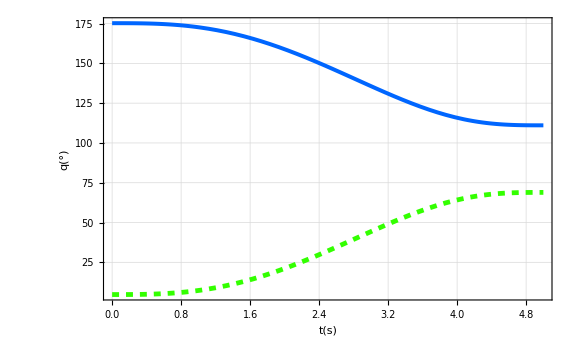
-Graphics-
-Graphics-

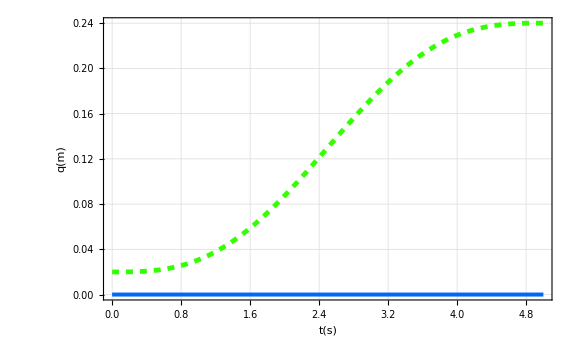
-Graphics-
-Graphics-

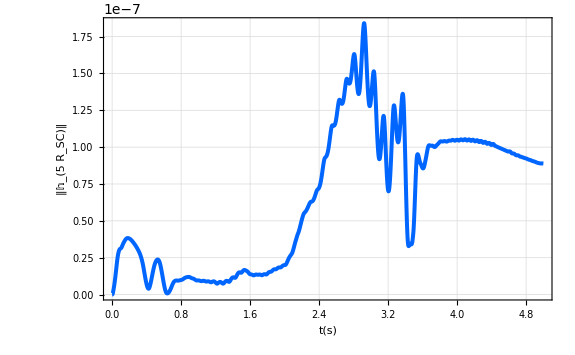
-Graphics-
-Graphics-

```mathematica
SPlot[(Mod[{Subscript[q, 1,Subscript[ℛ, 1]][t],Subscript[q, 2,Subscript[ℛ, 1]][t]},2π]/N[1Degree])/.S["ReferenceMotions"],{t,0,S["Time"]},{"t(s)","q(°)"},"",{"q_(1, SubscriptBox[ℛ, 1])","q_(2, SubscriptBox[ℛ, 1])"}]
SPlot[{Subscript[q, "5R_S",Subscript[𝓅, 1],1][t],Subscript[q, "5R_S",Subscript[𝓅, 1],2][t]}/.S["ReferenceMotions"],{t,0,S["Time"]},{"t(s)","q(m)"},"",{"q_(1, SubscriptBox[𝓅, 3], 1)","q_(1, SubscriptBox[𝓅, 3], 2)"}]
SPlot[Norm[Subscript[𝕙, "5R_SC"][t]/.S["ReferenceMotions"]/.S["Geometry"]],{t,0,S["Time"]},{"t(s)","‖𝕙_(5  R_SC)‖"},"",{}]
```

```mathematica
(*-Desired error dynamics-*)
(𝕧^★)_("5R_SC")[t_]=(Subscript[𝕡, "5R_SC"] '[t]/.S["ReferenceMotions"])+Subscript[𝕃, "5R_SC"]((Subscript[𝕡, "5R_SC"] [t]/.S["ReferenceMotions"])-(Subscript[𝕡, "5R_SC"] [t]))+Subscript[𝕂, "5R_SC"] SignA[((Subscript[𝕡, "5R_SC"] [t]/.S["ReferenceMotions"])-(Subscript[𝕡, "5R_SC"] [t]))+Subscript[𝕃, "5R_SC"]((Subscript[𝕢, "5R_SC"] [t]/.S["ReferenceMotions"])-(Subscript[𝕢, "5R_SC"] [t]))];

(*-Dynamic equations of controlled system-*)
Subscript[𝕕, "5R_SC"][t_]=Join[(𝕄^★)_("5R_SC")[t].(Subscript[𝕡, "5R_SC"] '[t]-(𝕧^★)_("5R_SC") [t]),Subscript[𝔸, "5R_SC"][t]. Subscript[𝕡, "5R_SC"] '[t]+Subscript[𝕓, "5R_SC"][t]+2 Subscript[β, "Baum2ζ"] Subscript[β, "Baum2ω"] Subscript[𝕙, "5R_SC"]'[t]+ Subscript[β, "Baum2ω"]^2 Subscript[𝕙, "5R_SC"][t]];
```

```mathematica
(*-Dynamic Simulation-*)
AppendTo[S,
"DynamicSimulation"-> Flatten[Quiet@NDSolve[Join[(#==0)&/@(Subscript[𝕕, "5R_SC"][t]/.S["Geometry"]/.S["Inertia"]/.S["ErrorDynamics"]/.S["Baumgarte"]),S["InitialState"]],Join[Subscript[𝕢, "5R_SC"] [t],Subscript[𝕡, "5R_SC"] [t],Subscript[𝕡, "5R_SC"] '[t]],{t,0,S["Time"]},Method->{"EquationSimplification"->"Residual"}]]
];
```

```mathematica
(*-Control inputs computations-*)
Module[{♢t,♢u,♢v},♢v=(((𝕄^★)_("5R_SC")[t].(𝕧^★)_("5R_SC") [t])/.S["Geometry"]/.S["Inertia"]/.S["ErrorDynamics"]/.S["DynamicSimulation"]);
♢u=(♢v/.{t-> #})&;
♢t=Range[0,S["Time"],S["Time"]/1000.];
♢v=Transpose[♢u/@♢t];
♢u=(Subscript[𝕦, "5R_SC"] [t]/.{♢var_[t]-> ♢var});
AppendTo[S,
"ControlInputs"-> ((♢u⟦#⟧-> Interpolation[MapThread[{#1,#2}&, {♢t,♢v⟦#⟧}]])&/@(Range@@Dimensions[Subscript[𝕦, "5R_SC"] [t]]))
];
]

Module[{♢t,♢u,♢v},♢v=(((𝕄^★)_("5R_SC")[t].Subscript[𝕡, "5R_SC"] '[t])/.S["Geometry"]/.S["Inertia"]/.S["ErrorDynamics"]/.S["ReferenceMotions"]);
♢u=(♢v/.{t-> #})&;
♢t=Range[0,S["Time"],S["Time"]/1000.];
♢v=Transpose[♢u/@♢t];
♢u=(Subscript[𝕦, "5R_SC"] [t]/.{♢var_[t]-> ♢var});
AppendTo[S,
"ComputedControlInputs"-> ((♢u⟦#⟧-> Interpolation[MapThread[{#1,#2}&, {♢t,♢v⟦#⟧}]])&/@(Range@@Dimensions[Subscript[𝕦, "5R_SC"] [t]]))
];
]
```

```mathematica
(Subscript[𝕂, "5R_SC"]/.S["ErrorDynamics"])
```

10.

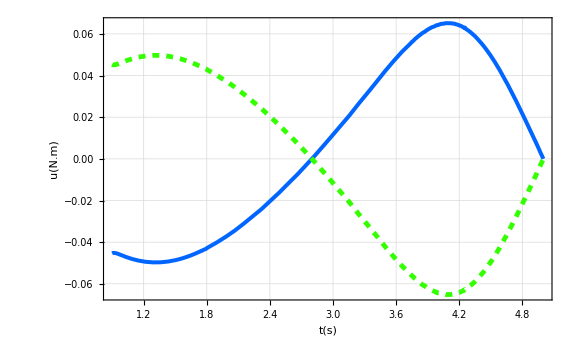
-Graphics-
-Graphics-

```mathematica
SPlot[{Subscript[u, 1,Subscript[ℛ, 1]][t],Subscript[u, 2,Subscript[ℛ, 1]][t]}/.S["ControlInputs"],{t,0.9,S["Time"]},{"t(s)","u(N.m)"},"",{"u_(1, SubscriptBox[ℛ, 1])","u_(2, SubscriptBox[ℛ, 1])"}]
```

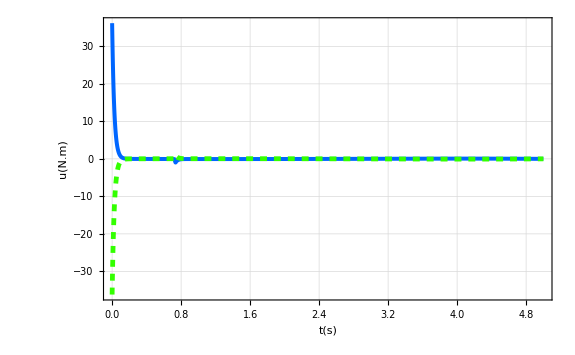
-Graphics-
-Graphics-

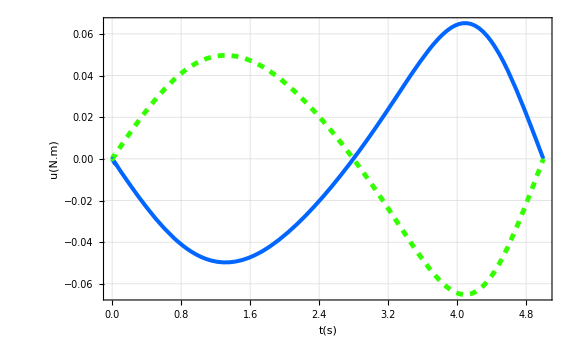
-Graphics-
-Graphics-

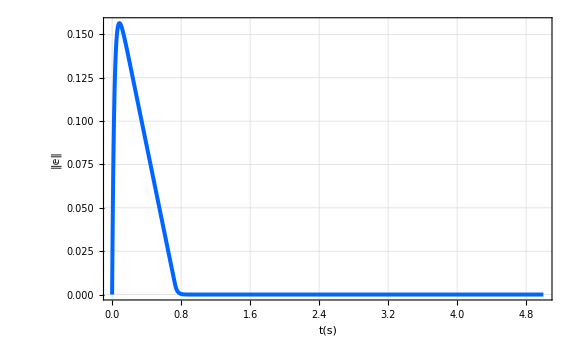
-Graphics-
-Graphics-

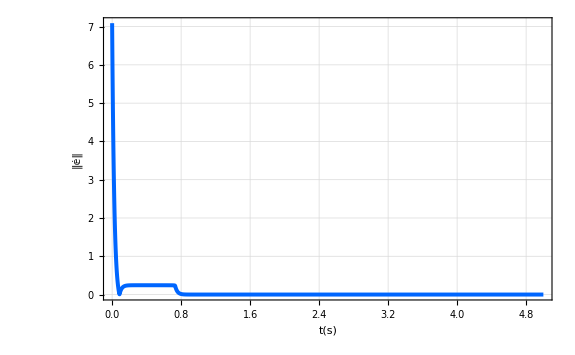
-Graphics-
-Graphics-

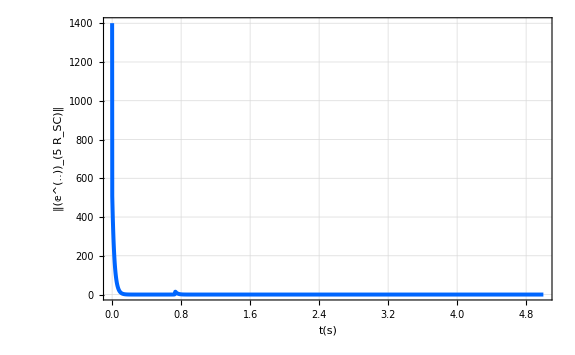
-Graphics-
-Graphics-

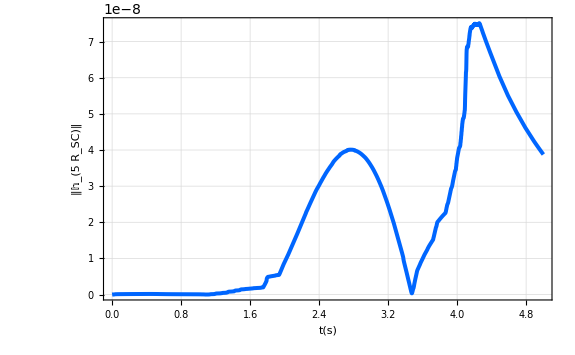
-Graphics-
-Graphics-

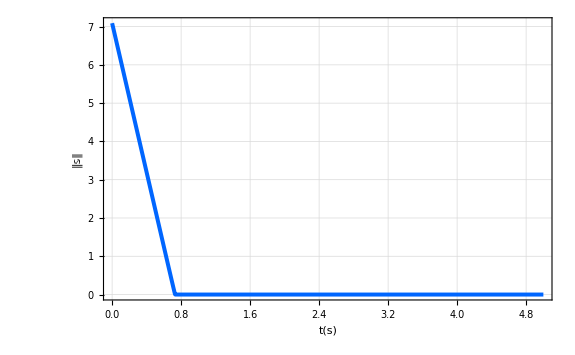
-Graphics-
-Graphics-

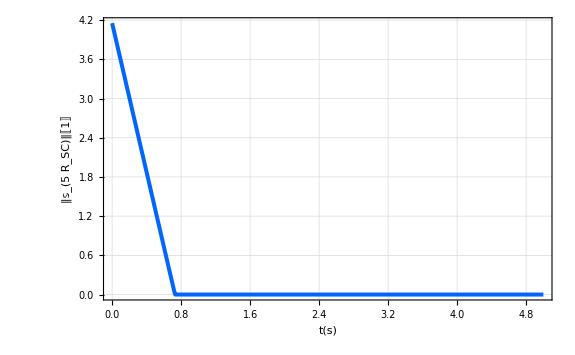
-Graphics-
-Graphics-

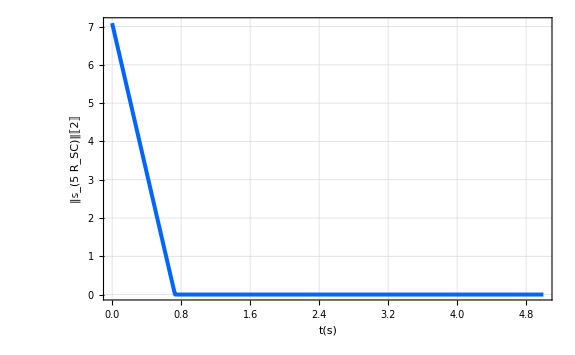
-Graphics-
-Graphics-

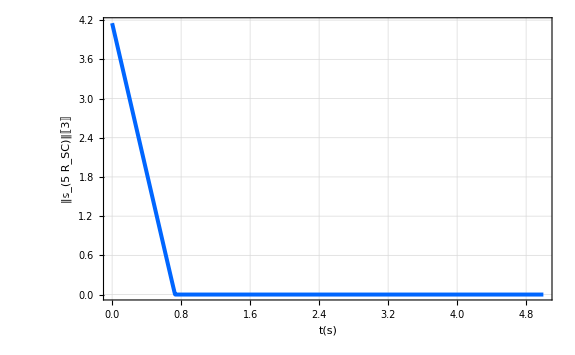
-Graphics-
-Graphics-

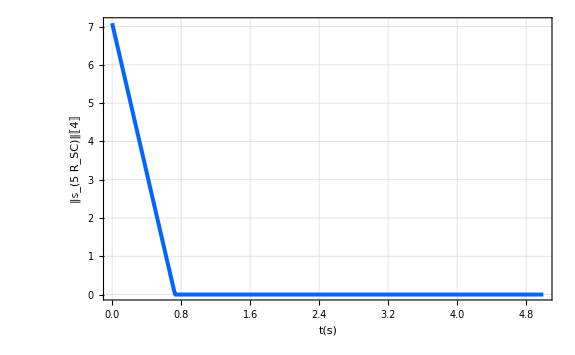
-Graphics-
-Graphics-

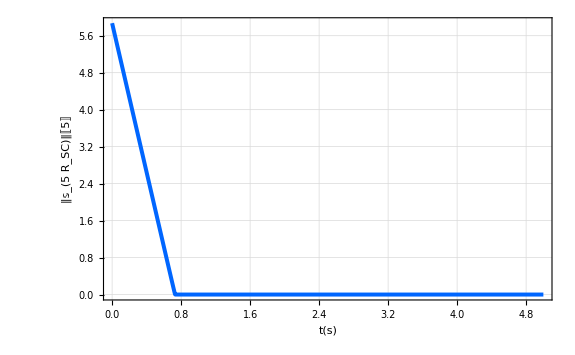
-Graphics-
-Graphics-

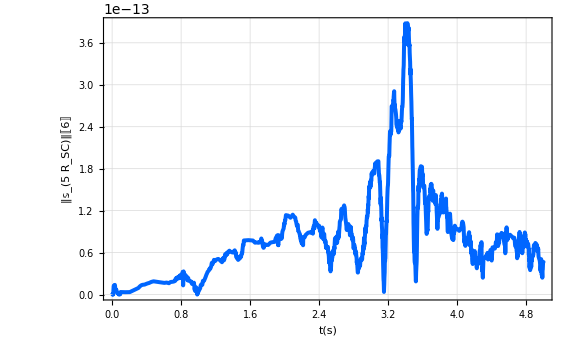
-Graphics-
-Graphics-

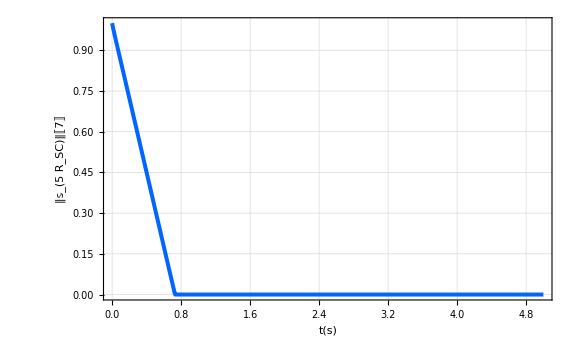
-Graphics-
-Graphics-

-Graphics-
-Graphics-

-Graphics-
-Graphics-

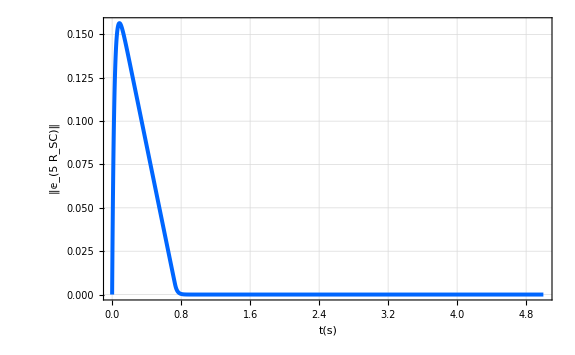
-Graphics-
-Graphics-

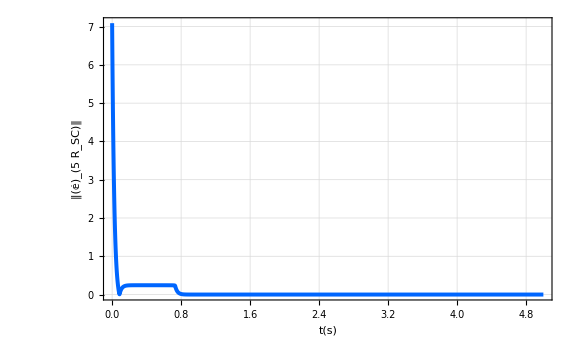
-Graphics-
-Graphics-

-Graphics-
-Graphics-

-Graphics-
-Graphics-

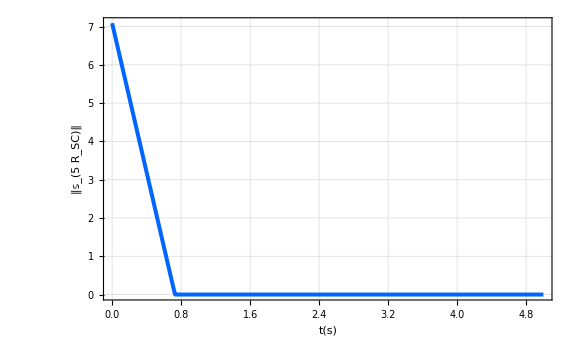
-Graphics-
-Graphics-

-Graphics-
-Graphics-

-Graphics-
-Graphics-

-Graphics-
-Graphics-

-Graphics-
-Graphics-

-Graphics-
-Graphics-

-Graphics-
-Graphics-

-Graphics-
-Graphics-

```mathematica
SPlot[{Subscript[u, 1,Subscript[ℛ, 1]][t],Subscript[u, 2,Subscript[ℛ, 1]][t]}/.S["ControlInputs"],{t,0,S["Time"]},{"t(s)","u(N.m)"},"",{"u_(1, SubscriptBox[ℛ, 1])","u_(2, SubscriptBox[ℛ, 1])"}]
SPlot[{Subscript[u, 1,Subscript[ℛ, 1]][t],Subscript[u, 2,Subscript[ℛ, 1]][t]}/.S["ComputedControlInputs"],{t,0,S["Time"]},{"t(s)","u(N.m)"},"",{"u_(1, SubscriptBox[ℛ, 1])","u_(2, SubscriptBox[ℛ, 1])"}]
SPlot[Norm[(Subscript[𝕢, "5R_SC"][t]/.S["ReferenceMotions"])-(Subscript[𝕢, "5R_SC"][t]/.S["DynamicSimulation"]), Infinity],{t,0,S["Time"]},{"t(s)","‖𝕖‖"},"",{}]
SPlot[Norm[(Subscript[𝕡, "5R_SC"][t]/.S["ReferenceMotions"])-(Subscript[𝕡, "5R_SC"][t]/.S["DynamicSimulation"]), Infinity],{t,0,S["Time"]},{"t(s)","‖𝕖̇‖"},"",{}]
SPlot[Norm[(Subscript[𝕡, "5R_SC"]'[t]/.S["ReferenceMotions"])-(Subscript[𝕡, "5R_SC"]'[t]/.S["DynamicSimulation"])],{t,0,S["Time"]},{"t(s)","‖(𝕖^(..))_(5  R_SC)‖"},"",{}]
SPlot[Norm[Subscript[𝕙, "5R_SC"][t]/.S["DynamicSimulation"]/.S["Geometry"]],{t,0,S["Time"]},{"t(s)","‖𝕙_(5  R_SC)‖"},"",{}]
SPlot[Norm[(Subscript[𝕡, "5R_SC"][t]/.S["ReferenceMotions"])-(Subscript[𝕡, "5R_SC"][t]/.S["DynamicSimulation"])+(Subscript[𝕃, "5R_SC"]/.S["ErrorDynamics"])((Subscript[𝕢, "5R_SC"][t]/.S["ReferenceMotions"])-(Subscript[𝕢, "5R_SC"][t]/.S["DynamicSimulation"])), Infinity],{t,0,S["Time"]},{"t(s)","‖𝕤‖"},"",{}]
SPlot[Norm[((Subscript[𝕡, "5R_SC"][t]/.S["ReferenceMotions"])-(Subscript[𝕡, "5R_SC"][t]/.S["DynamicSimulation"])+(Subscript[𝕃, "5R_SC"]/.S["ErrorDynamics"])((Subscript[𝕢, "5R_SC"][t]/.S["ReferenceMotions"])-(Subscript[𝕢, "5R_SC"][t]/.S["DynamicSimulation"])))⟦1⟧],{t,0,S["Time"]},{"t(s)","‖𝕤_(5  R_SC)‖⟦1⟧"},"",{}]
SPlot[Norm[((Subscript[𝕡, "5R_SC"][t]/.S["ReferenceMotions"])-(Subscript[𝕡, "5R_SC"][t]/.S["DynamicSimulation"])+(Subscript[𝕃, "5R_SC"]/.S["ErrorDynamics"])((Subscript[𝕢, "5R_SC"][t]/.S["ReferenceMotions"])-(Subscript[𝕢, "5R_SC"][t]/.S["DynamicSimulation"])))⟦2⟧],{t,0,S["Time"]},{"t(s)","‖𝕤_(5  R_SC)‖⟦2⟧"},"",{}]
SPlot[Norm[((Subscript[𝕡, "5R_SC"][t]/.S["ReferenceMotions"])-(Subscript[𝕡, "5R_SC"][t]/.S["DynamicSimulation"])+(Subscript[𝕃, "5R_SC"]/.S["ErrorDynamics"])((Subscript[𝕢, "5R_SC"][t]/.S["ReferenceMotions"])-(Subscript[𝕢, "5R_SC"][t]/.S["DynamicSimulation"])))⟦3⟧],{t,0,S["Time"]},{"t(s)","‖𝕤_(5  R_SC)‖⟦3⟧"},"",{}]
SPlot[Norm[((Subscript[𝕡, "5R_SC"][t]/.S["ReferenceMotions"])-(Subscript[𝕡, "5R_SC"][t]/.S["DynamicSimulation"])+(Subscript[𝕃, "5R_SC"]/.S["ErrorDynamics"])((Subscript[𝕢, "5R_SC"][t]/.S["ReferenceMotions"])-(Subscript[𝕢, "5R_SC"][t]/.S["DynamicSimulation"])))⟦4⟧],{t,0,S["Time"]},{"t(s)","‖𝕤_(5  R_SC)‖⟦4⟧"},"",{}]
SPlot[Norm[((Subscript[𝕡, "5R_SC"][t]/.S["ReferenceMotions"])-(Subscript[𝕡, "5R_SC"][t]/.S["DynamicSimulation"])+(Subscript[𝕃, "5R_SC"]/.S["ErrorDynamics"])((Subscript[𝕢, "5R_SC"][t]/.S["ReferenceMotions"])-(Subscript[𝕢, "5R_SC"][t]/.S["DynamicSimulation"])))⟦5⟧],{t,0,S["Time"]},{"t(s)","‖𝕤_(5  R_SC)‖⟦5⟧"},"",{}]
SPlot[Norm[((Subscript[𝕡, "5R_SC"][t]/.S["ReferenceMotions"])-(Subscript[𝕡, "5R_SC"][t]/.S["DynamicSimulation"])+(Subscript[𝕃, "5R_SC"]/.S["ErrorDynamics"])((Subscript[𝕢, "5R_SC"][t]/.S["ReferenceMotions"])-(Subscript[𝕢, "5R_SC"][t]/.S["DynamicSimulation"])))⟦6⟧],{t,0,S["Time"]},{"t(s)","‖𝕤_(5  R_SC)‖⟦6⟧"},"",{}]
SPlot[Norm[((Subscript[𝕡, "5R_SC"][t]/.S["ReferenceMotions"])-(Subscript[𝕡, "5R_SC"][t]/.S["DynamicSimulation"])+(Subscript[𝕃, "5R_SC"]/.S["ErrorDynamics"])((Subscript[𝕢, "5R_SC"][t]/.S["ReferenceMotions"])-(Subscript[𝕢, "5R_SC"][t]/.S["DynamicSimulation"])))⟦7⟧],{t,0,S["Time"]},{"t(s)","‖𝕤_(5  R_SC)‖⟦7⟧"},"",{}]
```

```mathematica
(*-Animation-*)
AppendTo[S,"Animation"-> Line[{{Subscript[q, 1,Subscript[𝓅, 0],1],Subscript[q, 1,Subscript[𝓅, 0],2]},{Subscript[q, 1,Subscript[𝓅, 0],1]+Cos[Subscript[q, 1,Subscript[ℛ, 1]][t]] Subscript[a, 1,1],Subscript[q, 1,Subscript[𝓅, 0],2]+Sin[Subscript[q, 1,Subscript[ℛ, 1]][t]] Subscript[a, 1,1]},{Subscript[q, "5R_S",Subscript[𝓅, 1],1][t],Subscript[q, "5R_S",Subscript[𝓅, 1],2][t]},{Subscript[q, 2,Subscript[𝓅, 0],1]+Cos[Subscript[q, 2,Subscript[ℛ, 1]][t]] Subscript[a, 2,1],Subscript[q, 2,Subscript[𝓅, 0],2]+Sin[Subscript[q, 2,Subscript[ℛ, 1]][t]] Subscript[a, 2,1]},{Subscript[q, 2,Subscript[𝓅, 0],1],Subscript[q, 2,Subscript[𝓅, 0],2]}}]];
SAnimationD=Graphics[{Orange, Thickness[0.008], S["Animation"]/.S["Geometry"]/.S["DynamicSimulation"]},PlotRange->{{-.25,+.25},{-.1,+.4}}]/.{t-> #}&;
SAnimationR=Graphics[{Green, Thickness[0.012], S["Animation"]/.S["Geometry"]/.S["ReferenceMotions"]},PlotRange->{{-.25,+.25},{-.1,+.4}}]/.{t-> #}&;
STrajectoryR=ParametricPlot[{Subscript[q, "5R_S",Subscript[𝓅, 1],1][t],Subscript[q, "5R_S",Subscript[𝓅, 1],2][t]}/.S["ReferenceMotions"],{t,0,S["Time"]},PlotRange->{{-.25,+.25},{-.1,+.4}},PlotStyle->{Pink,Thickness[0.005]}];
```

```mathematica
Manipulate[Show[STrajectoryR,SAnimationR[t] ,SAnimationD[t]],{t,0,S["Time"]}]
```

## UNBALANCED 5R MECHANISM

### UNBALANCED 5R MODEL (5R_U)

```mathematica
(*-Subsystems-*)
Subscript[Σ, "5R_U"]={1,2};
Subsystem["5R_U",1,"RR_U"] (*Subsystem 1: RR_U*)
Subsystem["5R_U",2,"RR_U"] (*Subsystem 2: RR_U*)

(*-System Variables-*)
Subscript[𝕢, "5R_U"][t_]=Join@@(Subscript[𝕢, "5R_U",#][t]&/@Subscript[Σ, "5R_U"]);
Subscript[𝕡, "5R_U"][t_]=Join@@(Subscript[𝕡, "5R_U",#][t]&/@Subscript[Σ, "5R_U"]);
```

```mathematica
(*-Additional constraints-*)
((𝕢̇)^★)_("5R_U")[t_]=Join@@(((𝕢̇)^★)_("5R_U",#)[t]&/@Subscript[Σ, "5R_U"]);
(𝕔^♁)_("5R_U") [t_]=({
Subscript[q, 1,Subscript[𝓅, 1],1]'[t]-Subscript[q, 2,Subscript[𝓅, 1],1]'[t],
Subscript[q, 1,Subscript[𝓅, 1],2]'[t]-Subscript[q, 2,Subscript[𝓅, 1],2]'[t]
}/.((𝕢̇)^★)_("5R_U")[t]);
(𝕔^★)_("5R_U")[t_]=DeleteCases[Join[Join@@((𝕔^★)_("5R_U",#)[t]&/@Subscript[Σ, "5R_U"]),(𝕔^♁)_("5R_U") [t]],0];

(*-Independent variables-*)
Subscript[𝕡^#, "5R_U"][t_]={Subscript[p, 1,Subscript[ℛ, 1]][t],Subscript[p, 2,Subscript[ℛ, 1]][t]};
(𝕡^♢)_("5R_U")[t_]=Complement[Subscript[𝕡, "5R_U"][t],Subscript[𝕡^#, "5R_U"][t]];
Subscript[Σ, 𝕡,"5R_U"]=Flatten[Position[Subscript[𝕡, "5R_U"][t],#]&/@Join[Subscript[𝕡^#, "5R_U"][t],(𝕡^♢)_("5R_U")[t]],Infinity];

(*-Additional constraints matrix-*)
Subscript[𝔹, "5R_U"][t_]=Transpose@(Join@@(Transpose@FullSimplify[D[(𝕔^♁)_("5R_U") [t],{Subscript[𝕡, "5R_U",#][t]}].Subscript[ℂ, "5R_U",#][t]]&/@Subscript[Σ, "5R_U"]));
Subscript[ℂ, "5R_U"][t_]=Transpose[FullSimplify@RowReduce[NullSpace[Subscript[𝔹, "5R_U"][t]]⟦All,Subscript[Σ, 𝕡,"5R_U"]⟧]⟦All,Subscript[Σ, 𝕡,"5R_U"]⟧];
Subscript[ℂ, "5R_U"][t](*//MatrixForm*)
Norm[Subscript[𝔹, "5R_U"][t].Subscript[ℂ, "5R_U"][t]//FullSimplify]
```

{{1,0},{-1-(Csc[q_(1,ℛ_1)[t]+q_(1,ℛ_2)[t]-q_(2,ℛ_1)[t]-q_(2,ℛ_2)[t]] Sin[q_(1,ℛ_1)[t]-q_(2,ℛ_1)[t]-q_(2,ℛ_2)[t]] a_(1,1))/(a_(1,2)),-(Csc[q_(1,ℛ_1)[t]+q_(1,ℛ_2)[t]-q_(2,ℛ_1)[t]-q_(2,ℛ_2)[t]] Sin[q_(2,ℛ_2)[t]] a_(2,1))/(a_(1,2))},{0,1},{(Csc[q_(1,ℛ_1)[t]+q_(1,ℛ_2)[t]-q_(2,ℛ_1)[t]-q_(2,ℛ_2)[t]] Sin[q_(1,ℛ_2)[t]] a_(1,1))/(a_(2,2)),-1-(Csc[q_(1,ℛ_1)[t]+q_(1,ℛ_2)[t]-q_(2,ℛ_1)[t]-q_(2,ℛ_2)[t]] Sin[q_(1,ℛ_1)[t]+q_(1,ℛ_2)[t]-q_(2,ℛ_1)[t]] a_(2,1))/(a_(2,2))}}

0

```mathematica
(*-Dynamic equations-*)
(𝕢^★)_("5R_U")[t_]={
Subscript[q, 1,Subscript[ℛ, 1]][t]+Subscript[q, 1,Subscript[ℛ, 2]][t]-Subscript[q, 2,Subscript[ℛ, 1]][t]-Subscript[q, 2,Subscript[ℛ, 2]][t]-> -Subscript[q, "5R_U",ℛ][t],
Subscript[q, 1,Subscript[ℛ, 1]][t]-Subscript[q, 2,Subscript[ℛ, 1]][t]-Subscript[q, 2,Subscript[ℛ, 2]][t]-> -Subscript[q, "5R_U",ℛ][t]-Subscript[q, 1,Subscript[ℛ, 2]][t],
Subscript[q, 1,Subscript[ℛ, 1]][t]+Subscript[q, 1,Subscript[ℛ, 2]][t]-Subscript[q, 2,Subscript[ℛ, 1]][t]-> -Subscript[q, "5R_U",ℛ][t]+Subscript[q, 2,Subscript[ℛ, 2]][t]
};
Subscript[ℂ, "5R_U"][t]/.(𝕢^★)_("5R_U")[t]//MatrixForm
Subscript[𝕕, "5R_U"][t_]=Simplify[Transpose[Subscript[ℂ, "5R_U"][t]/.(𝕢^★)_("5R_U")[t]].Join@@(Subscript[𝕕, "5R_U",#][t]&/@Subscript[Σ, "5R_U"])];
```

(1 | 0
-1-(Csc[q_(5R_U,ℛ)[t]] Sin[q_(1,ℛ_2)[t]+q_(5R_U,ℛ)[t]] a_(1,1))/(a_(1,2)) | (Csc[q_(5R_U,ℛ)[t]] Sin[q_(2,ℛ_2)[t]] a_(2,1))/(a_(1,2))
0 | 1
-(Csc[q_(5R_U,ℛ)[t]] Sin[q_(1,ℛ_2)[t]] a_(1,1))/(a_(2,2)) | -1+(Csc[q_(5R_U,ℛ)[t]] Sin[q_(2,ℛ_2)[t]-q_(5R_U,ℛ)[t]] a_(2,1))/(a_(2,2)))

```mathematica
(*-Inverse dynamics solution-*)
Subscript[𝕦^#, "5R_U"][t_]={Subscript[u, 1][t],Subscript[u, 2][t]};
(𝕦^★)_("5R_U")[t_]=Simplify[Flatten@Solve[(#==0)&/@Subscript[𝕕, "5R_U"][t],Subscript[𝕦^#, "5R_U"][t]]];
(*(𝕦^★)_("5R_U")[t]//TableForm*)
Subscript[𝕦^(★©), "5R_U"][t_]=Simplify[CoefficientArrays[Subscript[𝕦^#, "5R_U"][t]/.(𝕦^★)_("5R_U")[t],Subscript[𝕡, "5R_U"]'[t]]//Normal];
(𝕄^★)_("5R_U")[t_]=Subscript[𝕦^(★©), "5R_U"][t]⟦2⟧;
Subscript[𝕦^(★®), "5R_U"][t_]=Subscript[𝕦^(★©), "5R_U"][t]⟦1⟧;
(𝕄^★)_("5R_U")[t]ᵀ//MatrixForm
Subscript[𝕦^(★®), "5R_U"][t]//TableForm
```

((-Csc[q_(5R_U,ℛ)[t]] Sin[q_(1,ℛ_2)[t]+q_(5R_U,ℛ)[t]] a_(1,1) (Ι_(1,1)+Cos[q_(1,ℛ_2)[t]] Ι_(1,3))+a_(1,2) (Ι_(1,2)+Cos[q_(1,ℛ_2)[t]] Ι_(1,3)))/(a_(1,2)) | (Csc[q_(5R_U,ℛ)[t]] Sin[q_(2,ℛ_2)[t]] a_(2,1) (Ι_(1,1)+Cos[q_(1,ℛ_2)[t]] Ι_(1,3)))/(a_(1,2))
-(Csc[q_(5R_U,ℛ)[t]] Sin[q_(1,ℛ_2)[t]+q_(5R_U,ℛ)[t]] a_(1,1) Ι_(1,1))/(a_(1,2))+Cos[q_(1,ℛ_2)[t]] Ι_(1,3) | (Csc[q_(5R_U,ℛ)[t]] Sin[q_(2,ℛ_2)[t]] a_(2,1) Ι_(1,1))/(a_(1,2))
-(Csc[q_(5R_U,ℛ)[t]] Sin[q_(1,ℛ_2)[t]] a_(1,1) (Ι_(2,1)+Cos[q_(2,ℛ_2)[t]] Ι_(2,3)))/(a_(2,2)) | (Csc[q_(5R_U,ℛ)[t]] Sin[q_(2,ℛ_2)[t]-q_(5R_U,ℛ)[t]] a_(2,1) (Ι_(2,1)+Cos[q_(2,ℛ_2)[t]] Ι_(2,3))+a_(2,2) (Ι_(2,2)+Cos[q_(2,ℛ_2)[t]] Ι_(2,3)))/(a_(2,2))
-(Csc[q_(5R_U,ℛ)[t]] Sin[q_(1,ℛ_2)[t]] a_(1,1) Ι_(2,1))/(a_(2,2)) | (Csc[q_(5R_U,ℛ)[t]] Sin[q_(2,ℛ_2)[t]-q_(5R_U,ℛ)[t]] a_(2,1) Ι_(2,1))/(a_(2,2))+Cos[q_(2,ℛ_2)[t]] Ι_(2,3))

(-Csc[q_(5R_U,ℛ)[t]] Sin[q_(1,ℛ_2)[t]+q_(5R_U,ℛ)[t]] a_(1,1) a_(2,2) (Cos[q_(1,ℛ_1)[t]+q_(1,ℛ_2)[t]] 𝓂_(1,2)+Sin[q_(1,ℛ_2)[t]] Ι_(1,3) (p_(1,ℛ_1)[t])^2)+a_(1,2) (a_(2,2) (Cos[q_(1,ℛ_1)[t]] 𝓂_(1,1)-Sin[q_(1,ℛ_2)[t]] Ι_(1,3) (p_(1,ℛ_1)[t]+p_(1,ℛ_2)[t])^2)-Csc[q_(5R_U,ℛ)[t]] Sin[q_(1,ℛ_2)[t]] a_(1,1) (Cos[q_(2,ℛ_1)[t]+q_(2,ℛ_2)[t]] 𝓂_(2,2)+Sin[q_(2,ℛ_2)[t]] Ι_(2,3) (p_(2,ℛ_1)[t])^2)))/(a_(1,2) a_(2,2))
(Csc[q_(5R_U,ℛ)[t]] a_(2,1) (Sin[q_(2,ℛ_2)[t]] a_(2,2) (Cos[q_(1,ℛ_1)[t]+q_(1,ℛ_2)[t]] 𝓂_(1,2)+Sin[q_(1,ℛ_2)[t]] Ι_(1,3) (p_(1,ℛ_1)[t])^2)+Sin[q_(2,ℛ_2)[t]-q_(5R_U,ℛ)[t]] a_(1,2) (Cos[q_(2,ℛ_1)[t]+q_(2,ℛ_2)[t]] 𝓂_(2,2)+Sin[q_(2,ℛ_2)[t]] Ι_(2,3) (p_(2,ℛ_1)[t])^2))+a_(1,2) a_(2,2) (Cos[q_(2,ℛ_1)[t]] 𝓂_(2,1)-Sin[q_(2,ℛ_2)[t]] Ι_(2,3) (p_(2,ℛ_1)[t]+p_(2,ℛ_2)[t])^2))/(a_(1,2) a_(2,2))

### UNBALANCED 5R - SLIDING MODES CONTROL

```mathematica
(*-New variables-*)
Subscript[𝕦, "5R_UC"] [t_]={Subscript[u, 1,Subscript[ℛ, 1]][t],Subscript[u, 2,Subscript[ℛ, 1]][t]};
Subscript[𝕢, "5R_UC"] [t_]={Subscript[q, 1,Subscript[ℛ, 1]][t],Subscript[q, 1,Subscript[ℛ, 2]][t],Subscript[q, 2,Subscript[ℛ, 1]][t],Subscript[q, 2,Subscript[ℛ, 2]][t],Subscript[q, "5R_U",ℛ][t],Subscript[q, "5R_U",Subscript[𝓅, 1],1][t],Subscript[q, "5R_U",Subscript[𝓅, 1],2][t]};
Subscript[𝕡, "5R_UC"] [t_]={Subscript[q, 1,Subscript[ℛ, 1]]'[t],Subscript[q, 1,Subscript[ℛ, 2]]'[t],Subscript[q, 2,Subscript[ℛ, 1]]'[t],Subscript[q, 2,Subscript[ℛ, 2]]'[t],Subscript[q, "5R_U",ℛ]'[t],Subscript[q, "5R_U",Subscript[𝓅, 1],1]'[t],Subscript[q, "5R_U",Subscript[𝓅, 1],2]'[t]};
(𝕡^★)_("5R_UC")[t_]=Join[#,D[#,t]]&@{Subscript[p, 1,Subscript[ℛ, 1]][t]->Subscript[q, 1,Subscript[ℛ, 1]]'[t] ,Subscript[p, 1,Subscript[ℛ, 2]][t]-> Subscript[q, 1,Subscript[ℛ, 2]]'[t],Subscript[p, 2,Subscript[ℛ, 1]][t]-> Subscript[q, 2,Subscript[ℛ, 1]]'[t],Subscript[p, 2,Subscript[ℛ, 2]][t]-> Subscript[q, 2,Subscript[ℛ, 2]]'[t]};

(*-Holonomic constraint invariants-*)
Subscript[𝕙, "5R_UC"][t_]={
Subscript[q, 1,Subscript[ℛ, 1]][t]+Subscript[q, 1,Subscript[ℛ, 2]][t]-Subscript[q, 2,Subscript[ℛ, 1]][t]-Subscript[q, 2,Subscript[ℛ, 2]][t]+Subscript[q, "5R_U",ℛ][t],-Subscript[q, 1,Subscript[𝓅, 0],1]-Cos[Subscript[q, 1,Subscript[ℛ, 1]][t]] Subscript[a, 1,1]-Cos[Subscript[q, 1,Subscript[ℛ, 1]][t]+Subscript[q, 1,Subscript[ℛ, 2]][t]] Subscript[a, 1,2]+Subscript[q, "5R_U",Subscript[𝓅, 1],1][t],-Subscript[q, 1,Subscript[𝓅, 0],2]-Sin[Subscript[q, 1,Subscript[ℛ, 1]][t]] Subscript[a, 1,1]-Sin[Subscript[q, 1,Subscript[ℛ, 1]][t]+Subscript[q, 1,Subscript[ℛ, 2]][t]] Subscript[a, 1,2]+Subscript[q, "5R_U",Subscript[𝓅, 1],2][t],-Subscript[q, 2,Subscript[𝓅, 0],1]-Cos[Subscript[q, 2,Subscript[ℛ, 1]][t]] Subscript[a, 2,1]-Cos[Subscript[q, 2,Subscript[ℛ, 1]][t]+Subscript[q, 2,Subscript[ℛ, 2]][t]] Subscript[a, 2,2]+Subscript[q, "5R_U",Subscript[𝓅, 1],1][t],-Subscript[q, 2,Subscript[𝓅, 0],2]-Sin[Subscript[q, 2,Subscript[ℛ, 1]][t]] Subscript[a, 2,1]-Sin[Subscript[q, 2,Subscript[ℛ, 1]][t]+Subscript[q, 2,Subscript[ℛ, 2]][t]] Subscript[a, 2,2]+Subscript[q, "5R_U",Subscript[𝓅, 1],2][t]
};
{Subscript[𝕓, "5R_UC"][t_],Subscript[𝔸, "5R_UC"][t_]}=FullSimplify[Normal[CoefficientArrays[D[Subscript[𝕙, "5R_UC"][t],{t,2}],Subscript[𝕡, "5R_UC"]'[t]]]];

(*-Dynamic model-*)
Subscript[𝕦^(★©), "5R_UC"][t_]=Simplify[CoefficientArrays[Subscript[𝕦^#, "5R_U"][t]/.(𝕦^★)_("5R_U")[t]/.(𝕡^★)_("5R_UC")[t],Subscript[𝕡, "5R_UC"]'[t]]//Normal];
(𝕄^★)_("5R_UC")[t_]=Subscript[𝕦^(★©), "5R_UC"][t]⟦2⟧;
Subscript[𝕦^(★®), "5R_UC"][t_]=Subscript[𝕦^(★©), "5R_UC"][t]⟦1⟧;
```

```mathematica
(*-Simulation parameters-*)
U=<|
"Time"-> 5.0,
"Geometry"-> {
Subscript[a, 1,1]-> 0.1(*0.2*),Subscript[a, 1,2]-> 0.2,Subscript[q, 1,Subscript[𝓅, 0],1]-> -0.1,Subscript[q, 1,Subscript[𝓅, 0],2]-> 0.,
Subscript[a, 2,1]-> 0.1(*0.2*),Subscript[a, 2,2]-> 0.2,Subscript[q, 2,Subscript[𝓅, 0],1]-> +0.1,Subscript[q, 2,Subscript[𝓅, 0],2]-> 0.
},
"Inertia"->{
Subscript[Ι, 1,1]->Subscript[a, 2]^2 (Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 2]] Subscript[γ, 1,Subscript[ℬ, 2]]^2)+Subscript[Ι, 1,Subscript[ℬ, 2]]+Subscript[Ι, 2,Subscript[ℬ, 1]],
Subscript[Ι, 1,2]->Subscript[a, 1]^2 (Subscript[m, 1,Subscript[ℬ, 2]]+Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 1]] Subscript[γ, 1,Subscript[ℬ, 1]]^2)+Subscript[Ι, 1,Subscript[ℬ, 1]],
Subscript[Ι, 1,3]->Subscript[a, 1] Subscript[a, 2] (Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 2]] Subscript[γ, 1,Subscript[ℬ, 2]]),
Subscript[𝓂, 1,1]->g Subscript[a, 1] (Subscript[m, 1,Subscript[ℬ, 2]]+Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 1]] Subscript[γ, 1,Subscript[ℬ, 1]]),
Subscript[𝓂, 1,2]->g Subscript[a, 2] (Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 2]] Subscript[γ, 1,Subscript[ℬ, 2]]),
Subscript[Ι, 2,1]->Subscript[a, 2]^2 (Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 2]] Subscript[γ, 1,Subscript[ℬ, 2]]^2)+Subscript[Ι, 1,Subscript[ℬ, 2]]+Subscript[Ι, 2,Subscript[ℬ, 1]],
Subscript[Ι, 2,2]->Subscript[a, 1]^2 (Subscript[m, 1,Subscript[ℬ, 2]]+Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 1]] Subscript[γ, 1,Subscript[ℬ, 1]]^2)+Subscript[Ι, 1,Subscript[ℬ, 1]],
Subscript[Ι, 2,3]->Subscript[a, 1] Subscript[a, 2] (Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 2]] Subscript[γ, 1,Subscript[ℬ, 2]]),
Subscript[𝓂, 2,1]->g Subscript[a, 1] (Subscript[m, 1,Subscript[ℬ, 2]]+Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 1]] Subscript[γ, 1,Subscript[ℬ, 1]]),
Subscript[𝓂, 2,2]->g Subscript[a, 2] (Subscript[m, 2,Subscript[ℬ, 1]]+Subscript[m, 1,Subscript[ℬ, 2]] Subscript[γ, 1,Subscript[ℬ, 2]])
}//.{g-> 9.8,Subscript[a, 1]-> 0.1(*0.2*),Subscript[a, 2]-> 0.2,Subscript[m, 1,Subscript[ℬ, 1]]-> 0.2,Subscript[m, 1,Subscript[ℬ, 2]]-> 0.4,Subscript[m, 2,Subscript[ℬ, 1]]->1.5(*0.*),Subscript[m, 3,Subscript[ℬ, 1]]-> 0.,Subscript[m, 4,Subscript[ℬ, 1]]->0.,Subscript[Ι, 1,Subscript[ℬ, 1]]-> 0.00067,Subscript[Ι, 1,Subscript[ℬ, 2]]-> 0.00134,Subscript[Ι, 2,Subscript[ℬ, 1]]-> 0.,Subscript[γ, 1,Subscript[ℬ, 1]]-> 0.5,Subscript[γ, 1,Subscript[ℬ, 2]]-> 0.5,Subscript[γ, 1,Subscript[ℬ, 1]]-> 0.5},
"ErrorDynamics"-> {Subscript[𝕃, "5R_UC"]-> 40.,Subscript[𝕂, "5R_UC"]->10.},
"PrescribedCoordinates"->{Subscript[q, "5R_U",Subscript[𝓅, 1],1][t],Subscript[q, "5R_U",Subscript[𝓅, 1],2][t]},
"PrescribedMotions"->{Subscript[q, "5R_U",Subscript[𝓅, 1],1][t_]->0.+0.Cycloid[t,5.],Subscript[q, "5R_U",Subscript[𝓅, 1],2][t_]->0.02+0.22Cycloid[t,5.]}(*{Subscript[q, "5R_U",Subscript[𝓅, 1],1][t_]->0.06 Cos[20t],Subscript[q, "5R_U",Subscript[𝓅, 1],2][t_]-> 0.308+ 0.06 Sin[20t]}*),
"ReferenceInitialConfigurationEstimation"->{Subscript[q, "5R_U",ℛ][0]->N[2π/3],Subscript[q, 1,Subscript[ℛ, 1]][0]->N[3π/4],Subscript[q, 1,Subscript[ℛ, 2]][0]->-N[π/4],Subscript[q, 2,Subscript[ℛ, 1]][0]->N[π/4],Subscript[q, 2,Subscript[ℛ, 2]][0]->N[π/4]} ,
"InitialState"->{
Subscript[q, "5R_U",Subscript[𝓅, 1],1][0]==0.,
Subscript[q, "5R_U",Subscript[𝓅, 1],2][0]==0.02,
Subscript[q, "5R_U",ℛ][0]==15.590717970760307,
Subscript[q, 1,Subscript[ℛ, 1]][0]==21.90823175039844,
Subscript[q, 1,Subscript[ℛ, 2]][0]==-28.132794408983695,
Subscript[q, 2,Subscript[ℛ, 1]][0]==-18.766639096808646,
Subscript[q, 2,Subscript[ℛ, 2]][0]==28.132794408983695,
Subscript[q, "5R_U",Subscript[𝓅, 1],1]'[0]== 0.,
Subscript[q, "5R_U",Subscript[𝓅, 1],2]'[0]== 1.,
Subscript[q, "5R_U",ℛ]'[0]==-5.871084982536952,
Subscript[q, 1,Subscript[ℛ, 1]]'[0]==-4.153269558814007,
Subscript[q, 1,Subscript[ℛ, 2]]'[0]==7.0888120500824865,
Subscript[q, 2,Subscript[ℛ, 1]]'[0]==4.153269558814017,
Subscript[q, 2,Subscript[ℛ, 2]]'[0]==-7.088812050082491
}
(*{Subscript[q, 1,Subscript[ℛ, 1]][0]==1.6119296523430757,Subscript[q, 1,Subscript[ℛ, 2]][0]==-1.0404872392171414,Subscript[q, 2,Subscript[ℛ, 1]][0]==1.0181860217365257,Subscript[q, 2,Subscript[ℛ, 2]][0]==1.3635151903727818,Subscript[q, "5R_U",ℛ][0]==1.8102587989833734,Subscript[q, "5R_U",Subscript[𝓅, 1],1][0]==0.06,Subscript[q, "5R_U",Subscript[𝓅, 1],2][0]==0.308,Subscript[q, 1,Subscript[ℛ, 1]]'[0]==0,Subscript[q, 1,Subscript[ℛ, 2]]'[0]==0,Subscript[q, 2,Subscript[ℛ, 1]]'[0]==0,Subscript[q, 2,Subscript[ℛ, 2]]'[0]==0,Subscript[q, "5R_U",ℛ]'[0]==0,Subscript[q, "5R_U",Subscript[𝓅, 1],1]'[0]==0,Subscript[q, "5R_U",Subscript[𝓅, 1],2]'[0]==0}*),
"Baumgarte"-> {Subscript[β, "Baum1"]-> 10.0,Subscript[β, "Baum2ζ"]-> 1.,Subscript[β, "Baum2ω"]-> 1.}
|>;
```

```mathematica
(*-Initial configurations-*)
AppendTo[U,
"ReferenceInitialConfiguration"-> 
Join[((#/.{t->0})==(#/.U["PrescribedMotions"]/.{t->0}))&/@U["PrescribedCoordinates"],(Flatten[Quiet@FindRoot[Join[(#==0)&/@(Subscript[𝕙, "5R_UC"][t]/.U["Geometry"]/.U["PrescribedMotions"]/.{t-> 0})],Inner[{#1,#2}&,#,#/.U["ReferenceInitialConfigurationEstimation"],List]&@(Complement[Subscript[𝕢, "5R_UC"] [t],U["PrescribedCoordinates"]]/.{t-> 0})](*NSolve[Join[(#==0)&/@(Subscript[𝕙, "5R_UC"][t]/.U["Geometry"]/.U["PrescribedMotions"]/.{t-> 0})],(Complement[Subscript[𝕢, "5R_UC"] [t],U["PrescribedCoordinates"]]/.{t-> 0})]*)]/.{Rule-> Equal})]
];
```

```mathematica
(*-Reference motions-*)
AppendTo[U,
"ReferenceMotions"-> Flatten[Quiet@NDSolve[Join[((D[#,t])==(D[#/.U["PrescribedMotions"],t]))&/@U["PrescribedCoordinates"],(#==0)&/@(D[(Subscript[𝕙, "5R_UC"][t]/.U["Geometry"]/.U["PrescribedMotions"]),t]+(Subscript[β, "Baum1"] Subscript[𝕙, "5R_UC"][t])/.U["Geometry"]/.U["PrescribedMotions"]/.U["Baumgarte"]),U["ReferenceInitialConfiguration"]],Join[Subscript[𝕢, "5R_UC"] [t],Subscript[𝕡, "5R_UC"] [t],Subscript[𝕡, "5R_UC"] '[t]],{t,0,U["Time"]}]]
];
```

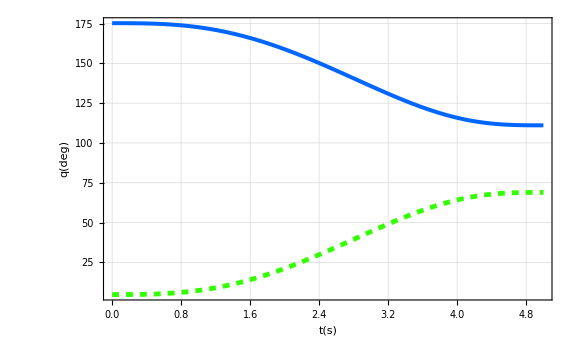
-Graphics-
-Graphics-

-Graphics-
-Graphics-

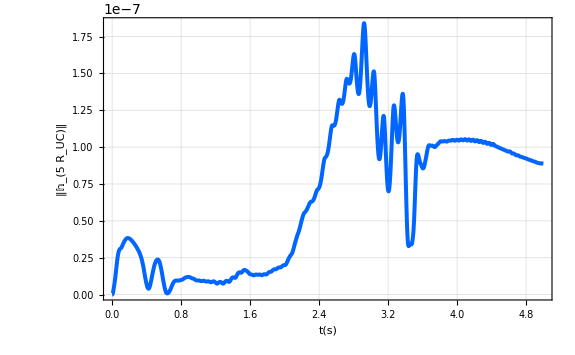
-Graphics-
-Graphics-

```mathematica
SPlot[(Mod[{Subscript[q, 1,Subscript[ℛ, 1]][t],Subscript[q, 2,Subscript[ℛ, 1]][t]},2π]/N[1Degree])/.U["ReferenceMotions"],{t,0,U["Time"]},{"t(s)","q(deg)"},"",{"q_(RR_U1, SubscriptBox[ℛ, 1])","q_(RR_S2, SubscriptBox[ℛ, 1])"}]
SPlot[{Subscript[q, "5R_U",Subscript[𝓅, 1],1][t],Subscript[q, "5R_U",Subscript[𝓅, 1],2][t]}/.U["ReferenceMotions"],{t,0,U["Time"]},{"t(s)","q(m)"},"",{"q_(5  R_U, SubscriptBox[𝓅, 1], 1)","q_(5  R_U, SubscriptBox[𝓅, 1], 2)"}]
SPlot[Norm[Subscript[𝕙, "5R_UC"][t]/.U["ReferenceMotions"]/.U["Geometry"]],{t,0,U["Time"]},{"t(s)","‖𝕙_(5  R_UC)‖"},"",{}]
```

```mathematica
(*-Desired error dynamics-*)
(𝕧^★)_("5R_UC")[t_]=(Subscript[𝕡, "5R_UC"] '[t]/.U["ReferenceMotions"])+Subscript[𝕃, "5R_UC"]((Subscript[𝕡, "5R_UC"] [t]/.U["ReferenceMotions"])-(Subscript[𝕡, "5R_UC"] [t]))+Subscript[𝕂, "5R_UC"] SignA[((Subscript[𝕡, "5R_UC"] [t]/.U["ReferenceMotions"])-(Subscript[𝕡, "5R_UC"] [t]))+Subscript[𝕃, "5R_UC"]((Subscript[𝕢, "5R_UC"] [t]/.U["ReferenceMotions"])-(Subscript[𝕢, "5R_UC"] [t]))];

(*-Dynamic equations of controlled system-*)
Subscript[𝕕, "5R_UC"][t_]=Join[(𝕄^★)_("5R_UC")[t].(Subscript[𝕡, "5R_UC"] '[t]-(𝕧^★)_("5R_UC") [t]),Subscript[𝔸, "5R_UC"][t]. Subscript[𝕡, "5R_UC"] '[t]+Subscript[𝕓, "5R_UC"][t]+2 Subscript[β, "Baum2ζ"] Subscript[β, "Baum2ω"] Subscript[𝕙, "5R_UC"]'[t]+ Subscript[β, "Baum2ω"]^2 Subscript[𝕙, "5R_UC"][t]];
```

```mathematica
(*-Dynamic Simulation-*)
AppendTo[U,
"DynamicSimulation"-> Flatten[Quiet@NDSolve[Join[(#==0)&/@(Subscript[𝕕, "5R_UC"][t]/.U["Geometry"]/.U["Inertia"]/.U["ErrorDynamics"]/.U["Baumgarte"]),U["InitialState"]],Join[Subscript[𝕢, "5R_UC"] [t],Subscript[𝕡, "5R_UC"] [t],Subscript[𝕡, "5R_UC"] '[t]],{t,0,U["Time"]},Method->{"EquationSimplification"->"Residual"}]]
];
```

```mathematica
(*-Control inputs computations-*)
Module[{♢t,♢u,♢v},♢v=(((𝕄^★)_("5R_UC")[t].(𝕧^★)_("5R_UC") [t]+Subscript[𝕦^(★®), "5R_UC"][t])/.U["Geometry"]/.U["Inertia"]/.U["ErrorDynamics"]/.U["DynamicSimulation"]);
♢u=(♢v/.{t-> #})&;
♢t=Range[0,U["Time"],U["Time"]/1000.];
♢v=Transpose[♢u/@♢t];
♢u=(Subscript[𝕦, "5R_UC"] [t]/.{♢var_[t]-> ♢var});
AppendTo[U,
"ControlInputs"-> ((♢u⟦#⟧-> Interpolation[MapThread[{#1,#2}&, {♢t,♢v⟦#⟧}]])&/@(Range@@Dimensions[Subscript[𝕦, "5R_UC"] [t]]))
];
]

Module[{♢t,♢u,♢v},♢v=(((𝕄^★)_("5R_UC")[t].Subscript[𝕡, "5R_UC"] '[t]+Subscript[𝕦^(★®), "5R_UC"][t])/.U["Geometry"]/.U["Inertia"]/.U["ErrorDynamics"]/.U["ReferenceMotions"]);
♢u=(♢v/.{t-> #})&;
♢t=Range[0,U["Time"],U["Time"]/1000.];
♢v=Transpose[♢u/@♢t];
♢u=(Subscript[𝕦, "5R_UC"] [t]/.{♢var_[t]-> ♢var});
AppendTo[U,
"ComputedControlInputs"-> ((♢u⟦#⟧-> Interpolation[MapThread[{#1,#2}&, {♢t,♢v⟦#⟧}]])&/@(Range@@Dimensions[Subscript[𝕦, "5R_UC"] [t]]))
];
]
```

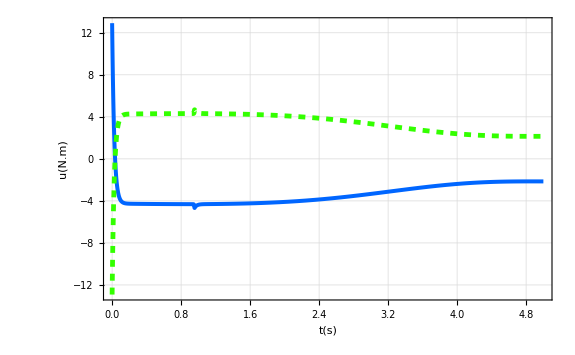
-Graphics-
-Graphics-

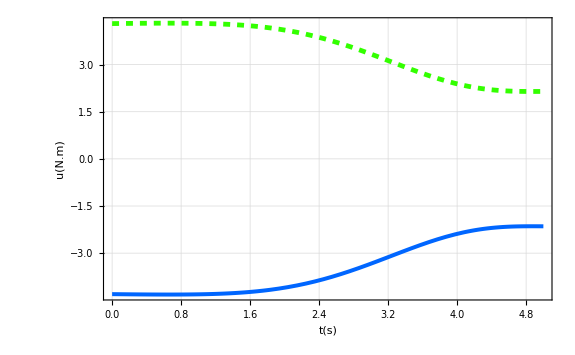
-Graphics-
-Graphics-

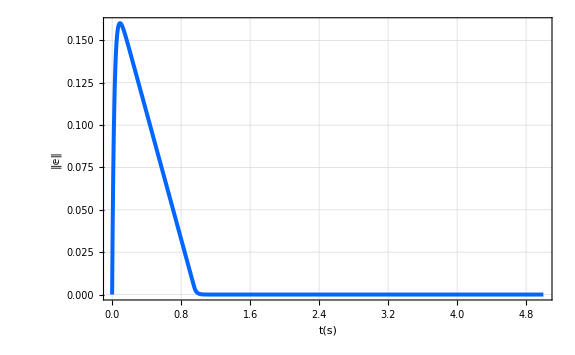
-Graphics-
-Graphics-

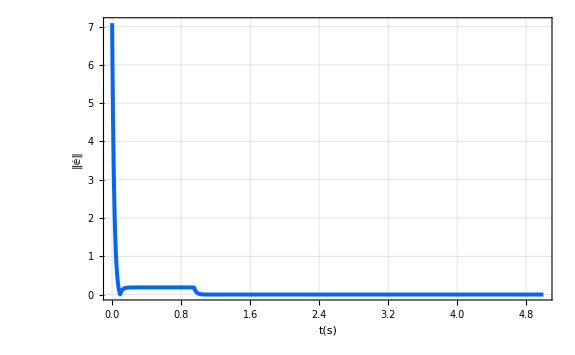
-Graphics-
-Graphics-

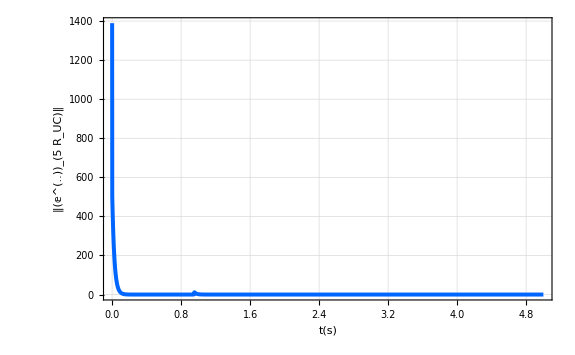
-Graphics-
-Graphics-

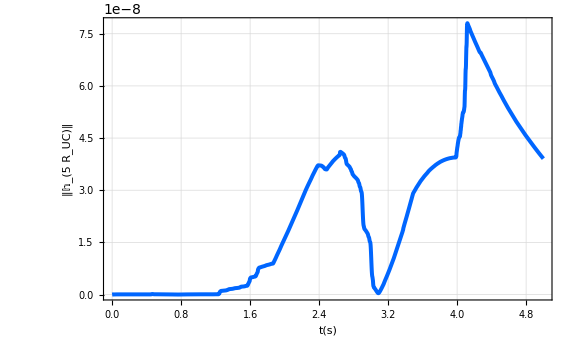
-Graphics-
-Graphics-

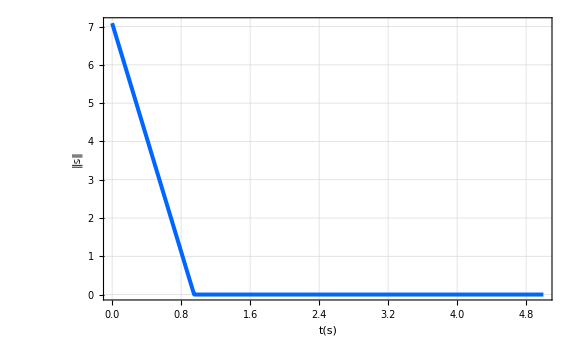
-Graphics-
-Graphics-

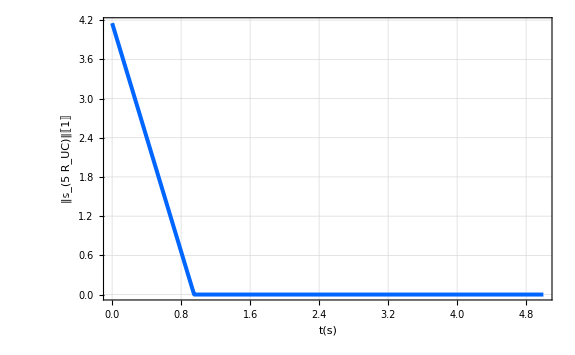
-Graphics-
-Graphics-

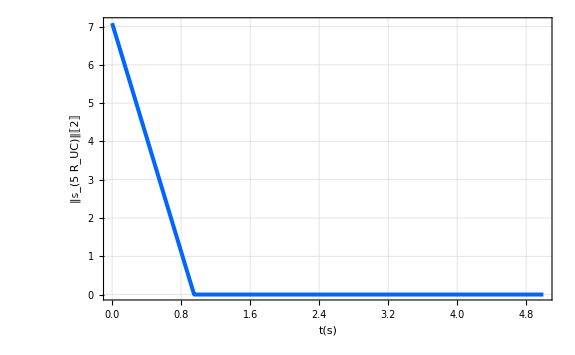
-Graphics-
-Graphics-

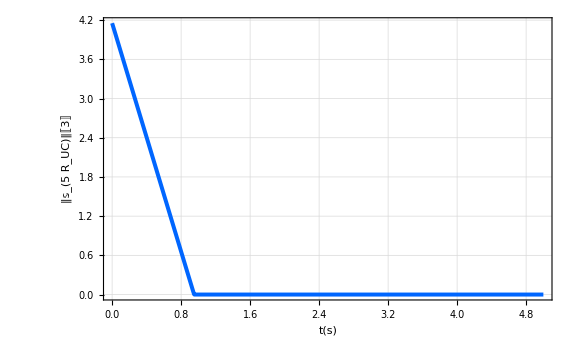
-Graphics-
-Graphics-

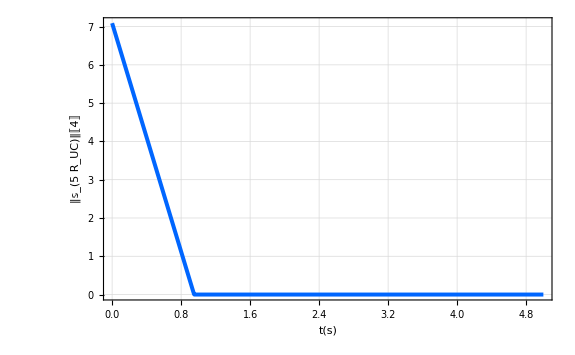
-Graphics-
-Graphics-

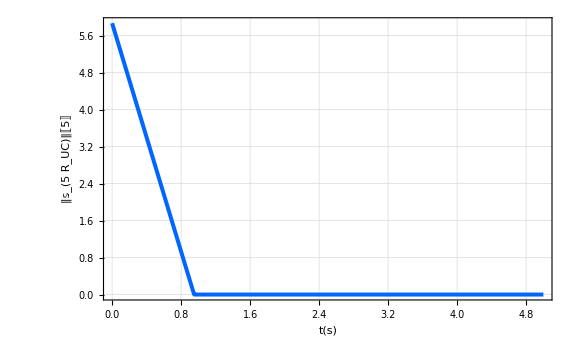
-Graphics-
-Graphics-

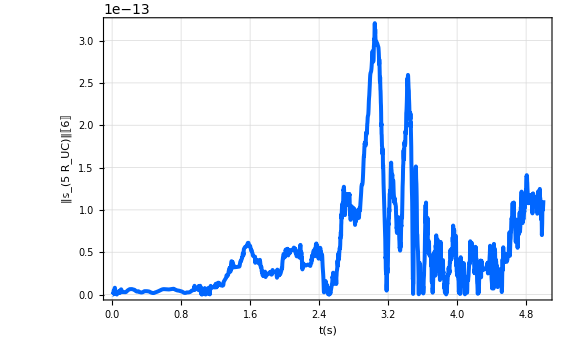
-Graphics-
-Graphics-

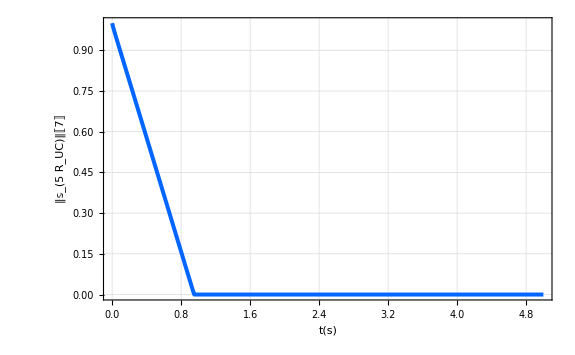
-Graphics-
-Graphics-

```mathematica
SPlot[{Subscript[u, 1,Subscript[ℛ, 1]][t],Subscript[u, 2,Subscript[ℛ, 1]][t]}/.U["ControlInputs"],{t,0,U["Time"]},{"t(s)","u(N.m)"},"",{"u_(1, SubscriptBox[ℛ, 1])","u_(2, SubscriptBox[ℛ, 1])"}]
SPlot[{Subscript[u, 1,Subscript[ℛ, 1]][t],Subscript[u, 2,Subscript[ℛ, 1]][t]}/.U["ComputedControlInputs"],{t,0,U["Time"]},{"t(s)","u(N.m)"},"",{"u_(1, SubscriptBox[ℛ, 1])","u_(2, SubscriptBox[ℛ, 1])"}]
SPlot[Norm[(Subscript[𝕢, "5R_UC"][t]/.U["ReferenceMotions"])-(Subscript[𝕢, "5R_UC"][t]/.U["DynamicSimulation"]),Infinity],{t,0,U["Time"]},{"t(s)","‖𝕖‖"},"",{}]
SPlot[Norm[(Subscript[𝕡, "5R_UC"][t]/.U["ReferenceMotions"])-(Subscript[𝕡, "5R_UC"][t]/.U["DynamicSimulation"]),Infinity],{t,0,U["Time"]},{"t(s)","‖𝕖̇‖"},"",{}]
SPlot[Norm[(Subscript[𝕡, "5R_UC"]'[t]/.U["ReferenceMotions"])-(Subscript[𝕡, "5R_UC"]'[t]/.U["DynamicSimulation"])],{t,0,U["Time"]},{"t(s)","‖(𝕖^(..))_(5  R_UC)‖"},"",{}]
SPlot[Norm[Subscript[𝕙, "5R_UC"][t]/.U["DynamicSimulation"]/.U["Geometry"]],{t,0,U["Time"]},{"t(s)","‖𝕙_(5  R_UC)‖"},"",{}]
SPlot[Norm[((Subscript[𝕡, "5R_UC"][t]/.U["ReferenceMotions"])-(Subscript[𝕡, "5R_UC"][t]/.U["DynamicSimulation"])+(Subscript[𝕃, "5R_UC"]/.U["ErrorDynamics"])((Subscript[𝕢, "5R_UC"][t]/.U["ReferenceMotions"])-(Subscript[𝕢, "5R_UC"][t]/.U["DynamicSimulation"]))),Infinity],{t,0,S["Time"]},{"t(s)","‖𝕤‖"},"",{}]
SPlot[Norm[((Subscript[𝕡, "5R_UC"][t]/.U["ReferenceMotions"])-(Subscript[𝕡, "5R_UC"][t]/.U["DynamicSimulation"])+(Subscript[𝕃, "5R_UC"]/.U["ErrorDynamics"])((Subscript[𝕢, "5R_UC"][t]/.U["ReferenceMotions"])-(Subscript[𝕢, "5R_UC"][t]/.U["DynamicSimulation"])))⟦1⟧],{t,0,S["Time"]},{"t(s)","‖𝕤_(5  R_UC)‖⟦1⟧"},"",{}]
SPlot[Norm[((Subscript[𝕡, "5R_UC"][t]/.U["ReferenceMotions"])-(Subscript[𝕡, "5R_UC"][t]/.U["DynamicSimulation"])+(Subscript[𝕃, "5R_UC"]/.U["ErrorDynamics"])((Subscript[𝕢, "5R_UC"][t]/.U["ReferenceMotions"])-(Subscript[𝕢, "5R_UC"][t]/.U["DynamicSimulation"])))⟦2⟧],{t,0,S["Time"]},{"t(s)","‖𝕤_(5  R_UC)‖⟦2⟧"},"",{}]
SPlot[Norm[((Subscript[𝕡, "5R_UC"][t]/.U["ReferenceMotions"])-(Subscript[𝕡, "5R_UC"][t]/.U["DynamicSimulation"])+(Subscript[𝕃, "5R_UC"]/.U["ErrorDynamics"])((Subscript[𝕢, "5R_UC"][t]/.U["ReferenceMotions"])-(Subscript[𝕢, "5R_UC"][t]/.U["DynamicSimulation"])))⟦3⟧],{t,0,S["Time"]},{"t(s)","‖𝕤_(5  R_UC)‖⟦3⟧"},"",{}]
SPlot[Norm[((Subscript[𝕡, "5R_UC"][t]/.U["ReferenceMotions"])-(Subscript[𝕡, "5R_UC"][t]/.U["DynamicSimulation"])+(Subscript[𝕃, "5R_UC"]/.U["ErrorDynamics"])((Subscript[𝕢, "5R_UC"][t]/.U["ReferenceMotions"])-(Subscript[𝕢, "5R_UC"][t]/.U["DynamicSimulation"])))⟦4⟧],{t,0,S["Time"]},{"t(s)","‖𝕤_(5  R_UC)‖⟦4⟧"},"",{}]
SPlot[Norm[((Subscript[𝕡, "5R_UC"][t]/.U["ReferenceMotions"])-(Subscript[𝕡, "5R_UC"][t]/.U["DynamicSimulation"])+(Subscript[𝕃, "5R_UC"]/.U["ErrorDynamics"])((Subscript[𝕢, "5R_UC"][t]/.U["ReferenceMotions"])-(Subscript[𝕢, "5R_UC"][t]/.U["DynamicSimulation"])))⟦5⟧],{t,0,S["Time"]},{"t(s)","‖𝕤_(5  R_UC)‖⟦5⟧"},"",{}]
SPlot[Norm[((Subscript[𝕡, "5R_UC"][t]/.U["ReferenceMotions"])-(Subscript[𝕡, "5R_UC"][t]/.U["DynamicSimulation"])+(Subscript[𝕃, "5R_UC"]/.U["ErrorDynamics"])((Subscript[𝕢, "5R_UC"][t]/.U["ReferenceMotions"])-(Subscript[𝕢, "5R_UC"][t]/.U["DynamicSimulation"])))⟦6⟧],{t,0,S["Time"]},{"t(s)","‖𝕤_(5  R_UC)‖⟦6⟧"},"",{}]
SPlot[Norm[((Subscript[𝕡, "5R_UC"][t]/.U["ReferenceMotions"])-(Subscript[𝕡, "5R_UC"][t]/.U["DynamicSimulation"])+(Subscript[𝕃, "5R_UC"]/.U["ErrorDynamics"])((Subscript[𝕢, "5R_UC"][t]/.U["ReferenceMotions"])-(Subscript[𝕢, "5R_UC"][t]/.U["DynamicSimulation"])))⟦7⟧],{t,0,S["Time"]},{"t(s)","‖𝕤_(5  R_UC)‖⟦7⟧"},"",{}]
```

```mathematica
(*-Animation-*)
AppendTo[U,"Animation"-> Line[{{Subscript[q, 1,Subscript[𝓅, 0],1],Subscript[q, 1,Subscript[𝓅, 0],2]},{Subscript[q, 1,Subscript[𝓅, 0],1]+Cos[Subscript[q, 1,Subscript[ℛ, 1]][t]] Subscript[a, 1,1],Subscript[q, 1,Subscript[𝓅, 0],2]+Sin[Subscript[q, 1,Subscript[ℛ, 1]][t]] Subscript[a, 1,1]},{Subscript[q, "5R_U",Subscript[𝓅, 1],1][t],Subscript[q, "5R_U",Subscript[𝓅, 1],2][t]},{Subscript[q, 2,Subscript[𝓅, 0],1]+Cos[Subscript[q, 2,Subscript[ℛ, 1]][t]] Subscript[a, 2,1],Subscript[q, 2,Subscript[𝓅, 0],2]+Sin[Subscript[q, 2,Subscript[ℛ, 1]][t]] Subscript[a, 2,1]},{Subscript[q, 2,Subscript[𝓅, 0],1],Subscript[q, 2,Subscript[𝓅, 0],2]}}]];
UAnimationD=Graphics[{Orange, Thickness[0.008], U["Animation"]/.U["Geometry"]/.U["DynamicSimulation"]},PlotRange->{{-.25,+.25},{-.1,+.4}}]/.{t-> #}&;
UAnimationR=Graphics[{Green, Thickness[0.012], U["Animation"]/.U["Geometry"]/.U["ReferenceMotions"]},PlotRange->{{-.25,+.25},{-.1,+.4}}]/.{t-> #}&;
UTrajectoryR=ParametricPlot[{Subscript[q, "5R_U",Subscript[𝓅, 1],1][t],Subscript[q, "5R_U",Subscript[𝓅, 1],2][t]}/.U["ReferenceMotions"],{t,0,U["Time"]},PlotRange->{{-.25,+.25},{-.1,+.4}},PlotStyle->{Pink,Thickness[0.005]}];
```

```mathematica
Manipulate[Show[UTrajectoryR,UAnimationR[t] ,UAnimationD[t]],{t,0,U["Time"]}]
```